# SCCC Mathematica Tutorial -- version 1.8

SCCC Mathematica Tutorial, © 2007-2017, Seattle Central Community College Math Dept., contact:  Greg.Langkamp@seattlecolleges.edu
Version 1.8/ August 2017

## Introduction

Purpose
This tutorial has been designed by the Mathematics Department at Seattle Central Community College to provide you with a complete, hands-on introduction to the basic commands that you will need to use Mathematica effectively in your math and science classes.  The six lessons of the tutorial will step you through each topic with many opportunities for you to practice and experiment with Mathematica.  The five appendices will provide additional information on how to use Mathematica effectively. It is expected that you will be able to work through the tutorial on your own with minimal help in a relatively short time.

Mathematical Level Required
The tutorial was developed to provide a thorough and efficient introduction to Mathematica for students about to enter a Calculus course. Therefore the tutorial only assumes familiarity with mathematics at the Precalculus level.

Structure
The basic part of the tutorial is divided into six lessons. Each lesson is divided further into subsections devoted to specific topics and corresponding Mathematica commands. Following most subsections there is a set of exercises. These are short practice problems based on the material from the section.  Answers are provided for all exercises so that you can check your work. 

The first lesson covers the material that is typically presented during the introductory lecture in the first class session of CSC 102Q.  Subsequent lessons cover the basic commands relating to numerical calculation, algebra, functions, graphing and solving equations.  Everything that you will need to use Mathematica in your math class is covered.

Format
This tutorial has been specially formatted to aid the new user in learning Mathematica.  Here are some things to be aware of.

1. The tutorial opens at 125 % magnification. You can change the magnification to suit your needs by clicking on the bottom right of the screen. (You may need to maximize the tutorial window first.)

2. The tutorial lessons are presented in a collapsible outline form.  You have the option of opening all the sections at once if you prefer to work on the tutorial this way. Likewise, you can collapse all of the sections of the tutorial in one step. Instructions on both of these operations are given below.  

	To open all subsections: 
		a.  Choose Edit from the Menu and then Select All
		b.  Choose Cell, then Grouping, then Open All Subgroups
	To close all subsections: 
		a.  Choose Edit from the Menu and then Select All  
		b.  Choose Cell, then Grouping, then Close All Subgroups	
	
3.  The text font used in this tutorial is “Comic Sans MS”.

## Lesson 1 Numerical Computation

### 1.1 How to enter a simple numerical calculation

Using Mathematica to do numerical calculations is very straightforward. Just enter the expression and then press ⇧[⌤]  (hold down the Shift key, then press Enter). We will refer to pressing ⇧[⌤] as "evaluating" the input. The result of the calculation will appear in a math output cell.

Enter 2 + 2 in the math input cell below and then press ⇧[⌤] (hold down the Shift key, then press Enter).

Another way to evaluate an input
Some keyboards have an Enter key at the extreme right of the keyboard, next to a numeric keypad. This Enter key can be pressed without pressing Shift.

Click anywhere in the input cell below and then press the Enter key on the extreme right of the keyboard.

```mathematica
1+2+3+4+5
```

Modifying an input to create a new input
Note that any Mathematica input cell can be changed and reevaluated.  Change the 5 in the input above to 500 and then evaluate the revised input. Observe that the output automatically updates to reflect the new input.

Creating a new input cell
If you pass your mouse vertically over the screen you will see that the edit cursor is vertical (looks like an I-beam) when passing over text cells and existing input and output cells, but switches to a horizontal edit cursor in the spaces between these cells.  At any point where the cursor is horizontal you can click on the screen and Mathematica will draw a faint horizontal line. Just start typing and a new math input cell is automatically created. Try doing this now above the gray box below.

Enter a new math input cell above this gray box ↑↑↑↑

Deleting math input cells
Occasionally you will create a few extra math input cells that you want to get rid off.  To delete cells, click on the cell bracket icon -Graphics- on the far right side of the screen. Then press the Delete key on your keyboard.  Practice this now by deleting the two math input cells below.

Below are two exercises for practice. Give them a try!

##### Exercise 1.1 A

Evaluate the expression (3.56^2+4.53^4)/34.87. Enter this just as you would on a calculator (use " / " for division). Don't forget to enclose the entire numerator in parentheses.

```mathematica
(3.56^2+4.53^3)/34.87
```

3.02935

Answer to Exercise 1.1A

```mathematica
(3.56^2 + 4.53^4)/34.87
```

##### Exercise 1.1 B

Create a new input cell with the expression 5 + 9 between the two text cells below.  Move the mouse from one text cell down to the other and click and start typing when the cursor is horizontal.

Put your new input cell below this text cell  ↓↓↓↓↓↓↓↓↓ ...

..and above this text cell ↑↑↑↑↑↑↑↑↑

Answer to Exercise 1.1B

This is what it should look like when you  are done.

Put your new input cell below this text cell  ↓↓↓↓↓↓↓↓↓ ....

```mathematica
5 + 9
```

... and above this text cell ↑↑↑↑↑↑↑↑↑

### 1.2 Exact vs. numerical approximations -- using the "N" command

Calculate the value of 34^19.   In the input cell below, enter the expression 34^19, then press ⌤.

```mathematica
34^19
```

125342809160496617801464152064

Note that Mathematica produces the exact answer here; all thirty digits!  Mathematica will always display the exact value when doing a calculation if it is possible to do so.  However, if we really just want a numerical approximation, then we can use the "N" command as shown below.  Here "N" stands for "numerical".

Click anywhere in math input cell below and press ⌤. (Note the use of square brackets in the command below. Square brackets are used in all Mathematica commands).

```mathematica
N[34^19]
```

1.25343×10^29

Here the answer is expressed using scientific notation with a default of 6 significant digits. To get more digits, we just add a second argument to the command. For example, if we want 25 digits we enter N[34^19, 25].

Click anywhere in the math input cell below and press ⌤.

```mathematica
N[34^19,25]
```

Note that the command above has two "arguments" (or inputs) namely 34^19 and 25. These are separated by a comma. This is standard syntax for Mathematica commands that have more than one argument.

When entering a command it's okay to put in some extra spaces as in the next input cell.

```mathematica
N[  34^19   , 25  ]
```

### 1.3 Adding fractions

Add the fractions 2/3+5/7 by evaluating the input cell below.

```mathematica
2/3 + 5/7
```

Again Mathematica gives us the exact answer rather than a decimal approximation.

##### Exercise 1.3 A

Find a 100 digit approximation for the sum of the fractions 2/3+5/7.

```mathematica
N[2/3+5/7,100]
```

1.380952380952380952380952380952380952380952380952380952380952380952380952380952380952380952380952381

Answer to Exercise 1.3A

```mathematica
N[2/3 + 5/7, 100]
```

💡 Math fact: The fraction  29/21 is by definition a rational number. Recall that rational numbers are always expressible as either terminating decimals (e.g. 3/4=.75) ... or repeating, nonterminating decimals (e.g. 1/3=.333333...). What can you say about 29/21?

### 1.4 Another way to apply the N command

In Section 1.2 you learned about the N command which produces numerical approximations.  Recall that Mathematica will produce the exact answer for a calculation whenever possible. This sometimes produces surprising results.

Execute the input below.

```mathematica
(987^17 - 85^20)/1452
```

400277888077179353778265023820771945807775583659221/726

Well, there it is, the exact answer! This is the exact, reduced fraction which is equal to our input.  In cases like this we almost always prefer Mathematica to give us a numerical approximation.

Earlier we applied the N command to our original expression as in the input cell below. Execute this cell.

```mathematica
N[(987^17 - 85^20)/1452]
```

5.51347×10^47

In the input cell below, we introduce an alternative way to achieve the same result. This is called "postfix" (as contrasted to "prefix") form, since here the command follows, rather than precedes, the argument. Note the use of the double forward slash " // ".  Execute this cell.

```mathematica
(987^17 - 85^20)/1452//N
```

5.51347×10^47

Prefix vs. Postfix 
Postfix form is often convenient, however it does have one significant limitation. It is not possible to specify options for a command when using the postfix form. So, for example, if you want π displayed with 20 digits then you will need to use N[π,20] . There is no way to use //N and at the same time specify that you want 20 digits.

### 1.5 Representing the numbers π and ⅇ in Mathematica

In Mathematica we can enter the constant π  by using the keyboard shortcut Esc p Esc. (You will find the Esc key at the upper left-hand corner of your keyboard).

Enter π in the input cell below by using the keyboard shortcut Esc p Esc.  (Observe that when you press the Esc key it appears as  , then you enter p, and when you press the Esc key the second time, the π symbol magically appears).

Find the first 1000 digits of π.  Note the next line is entered N[EscpEsc,1000].

```mathematica
N[π, 1000]
```

What to do if Mathematica freezes up...
Occasionally you will find that Mathematica  gets "hung up" or "frozen" while working on some computation.  Here is the first thing to try to remedy the problem:   Click on the Evaluation pull-down menu at the top of the notebook, then select Abort > Evaluation.  (The short-cut is ALT + comma).  

If that does not work, the second option is to select Quit Kernel - Local.   Quitting the kernel turns off the mathematical engine that runs in the background without closing down all of Mathematica.  You can start right up again by executing any math input cell by pressing ENTER.

The final option would be to shut down Mathematica.  Doing this, though, will lost any unsaved work so try the above options first!

In Mathematica, we can enter the exponential constant (i.e., the base of the natural logarithm) ,  ⅇ ≈ 2.71828 , by using the keyboard shortcut Esc ee Esc.  Note that you must use two e's.  If you use just one e,  you will get the symbol ϵ for the Greek letter epsilon.  Try entering ⅇ using the keyboard shortcut in the math input cell below.

Enter  ⅇ  in the input cell below by using the keyboard shortcut Esc ee Esc.

```mathematica
ⅇ
```

ⅇ

☑ Mathematica  has simple shortcuts for the Greek alphabet. Here some common ones that you may want to use.

alpha | α | Esc a Esc
beta | β | Esc b Esc
gamma | γ | Esc g Esc
delta | δ | Esc d Esc
epsilon | ϵ | Esc e Esc
theta | θ | Esc th Esc
kappa | κ | Esc k Esc
lambda | λ | Esc l Esc
pi | π | Esc p Esc
omega | ω | Esc o Esc

Exercise 1.5 A

Multiple choice question.
Which of the following will give us the exponential constant  ⅇ ≈ 2.71828 ?
A.          e
B.   Esc e Esc
C.   Esc ee Esc

##### Answer to Exercise 1.5A

A.          e		☹  WRONG! 	This is just the letter e. 
B.    Esc e Esc	    ☹ WRONG! 	        This gives the Greek letter epsilon ϵ.
C.   Esc ee Esc  	    ☺  RIGHT !!

Exercise 1.5 B

Look at the first two thousand digits of ⅇ.  Given that ⅇ is an irrational number what should we expect to see (or not see) when we look at this decimal?

```mathematica
N[ⅇ,2]
```

2.7

##### Answer to Exercise 1.5B

```mathematica
N[ⅇ, 2000]
```

💡Math fact: Since ⅇ is an irrational number it is a nonrepeating, nonterminating decimal. Therefore we should expect to see a decimal that goes on forever with no repeating sequence of digits.

### 1.6 A keyboard shortcut for entering square roots

If you need to enter a square root on your calculator you simply press the button with the square root symbol √. . Unfortunately, standard computer keyboards don't have a square root key.  But Mathematica does have a special keyboard shortcut which allows you to enter a square root symbol.  To enter a square root enter Ctrl[2] , (that is, while holding down the Control key, type the number 2).  The result is the square root template √□.  If you now enter a number, while the small entry box is still highlighted, it will be placed under the radical.

To enter the expression √49, enter  Ctrl[2] 49.  Try this below.

```mathematica
√49.
```

7.

### 1.7 Decimals in -- decimals out

Mathematica employs a useful convention when doing numerical calculations. If your input contains any numbers in decimal form then it automatically produces an answer in decimal form. This is an alternative way to get a numerical approximation without using the "N" command.

Compare the outputs resulting from entering √90 and √90. below.  Observe that the mere presence of the decimal point in the second radical is enough to change the output form from exact to decimal.

```mathematica
√90
```

3 √10

```mathematica
√90.
```

9.48683

Here is another example. Note that if any part of the input contains a decimal then the output will be displayed in decimal form.

```mathematica
12 + 1/2 + 23 + 2^2.3
```

40.4246

### 1.8 Numerical lists -- the Range command

The Range command allows you to quickly generate a list of numbers. Here are some examples of how it works.
The basic syntax is:   Range[ start, end, increment]

Generate a list of numbers starting with 10 ending with 200 in increments of 2.

```mathematica
Range[10, 200, 2]
```

Generate a list of numbers starting with 1, ending with 10 in increments of .5.

```mathematica
Range[1, 10, 0.5]
```

Generate a list of numbers starting with 0, ending with π in increments of π/16.

```mathematica
Range[0, π, π/16]
```

If you leave out the increment, it is assumed to be 1 . That is, Range[ a, b] is equivalent to Range[a, b, 1] (see below).

```mathematica
Range[-2,8]
```

If you want to generate a list of positive integers, starting with 1, up to some particular integer, then you can use the shorter form below. That is, Range[n] is equivalent to Range[1,n,1] and Range[1,n].

```mathematica
Range[20]
```

If you apply an arithmetic operation to a list and the operation will be performed on each element of the list.

Find the square of all the positive integers from 1 to 25.

```mathematica
Range[25]^2
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625}

Exercise 1.8 A

Create a list that consists of all the integers from -10 to 10.

```mathematica
Range[-10,10,1]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

##### Answer to Exercise 1.8A

```mathematica
Range[-10,10,1]
```

Or we could use the shorter form.

```mathematica
Range[-10, 10]
```

Exercise 1.8 B

Create a list that consists of all the even numbers from 12 to 56.

```mathematica
Range[12,56,2]
```

{12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56}

##### Answer to Exercise 1.8B

```mathematica
Range[12, 56, 2]
```

Exercise 1.8 C

Create a list that consists of the cubes of the integers from 1 to 15.

```mathematica
Range[15]^3
```

{1,8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375}

##### Answer to Exercise 1.8C

```mathematica
Range[15]^3
```

## Lesson 2 Standard Mathematical Functions

### 2.1 Introduction

Mathematica  has thousands of built-in mathematical functions.  In this lesson we will focus on the functions that you are already familiar with from Precalculus; namely trigonometric, exponential and logarithmic functions.

There are two important rules that you need to remember when using Mathematica's built-in functions. 
1.  All functions start with a capital letter.
2. All functions use square brackets (not parentheses) to enclose their input value.

The Absolute Value and Square Root Functions
A simple example of the application of these rules is the absolute value function.  On most calculators the absolute value function | x| is represented by the function abs(x). The corresponding function in Mathematica is Abs[x] . Note that we start with a capital letter and use square brackets.

```mathematica
Abs[-6]
```

Earlier, we introduced the keyboard shortcut Ctrl[2] to enter a square root.  So to enter the square root function we would enter the keystrokes Ctrl[2] x.

```mathematica
√x
```

The square root function √x is also represented in Mathematica by the built-in function Sqrt[x] (note that this function starts with a capital letter S).  So the two expressions below are equivalent. You can use either, although in this tutorial we will continue to use the keyboard shortcut.

```mathematica
√36
```

```mathematica
Sqrt[36]
```

### 2.2 Trigonometric functions

Use Mathematica to evaluate sin(π/3). Recall that the keyboard shortcut for π is Esc p Esc.  We use Sin for the function name and enclose the input in square brackets.

```mathematica
Sin[π/3]
```

Unlike a calculator, Mathematica gives an exact value.

The table below shows the syntax for the other trigonometric functions. Note that each function on the right starts with a capital letter and uses square brackets to enclose the function input.

to get this, | we enter this:
sin(x) | Sin[x]
cos(x) | Cos[x]
tan(x) | Tan[x]
csc(x) | Csc[x]
sec(x) | Sec[x]
cot(x) | Cot[x]
sin^-1(x) | ArcSin[x]
cos^-1(x) | ArcCos[x]
tan^-1(x) | ArcTan[x]

⚠ Caution: Note that for the inverse functions two letters are capitalized; e.g., both A and T are capitalized in ArcTan.

Use the table above and the keyboard shortcut for π to enter and evaluate each of the following expressions.

Evaluate cos(π/4)

```mathematica
Cos[π/4]
```

1/(√2)

value = 1/(√2)

Evaluate sec(π/4)

```mathematica
Sec[π/4]
```

√2

value = √2

Evaluate tan(π/4)

```mathematica
Tan[π/4]
```

1

value = 1

Evaluate tan^-1(1)

```mathematica
ArcTan[1]
```

π/4

value = π/4

Raising a trigonometric function to a power
Suppose you want to enter a power of trigonometric function such as sin^2(π/3). The correct Mathematica syntax in this case is:  Sin[π/3]^2 .  Note in particular that you must place the exponent after the argument, [π/3],  and not directly after the Sin. So the keystrokes for entering sin^2(π/3) are: Sin[ π/3] ^ 2 . Try this below.

```mathematica
Sin[π/3]^2
```

3/4

Evaluate cos^3(π/4).  If you enter this correctly you should get 1/(2 √2) as an output.

```mathematica
Cos[π/4]^3
```

1/(2 √2)

Radians vs. Degrees
All trigonometric functions in Mathematica are based on radians. However there is an easy way to enter angles in degrees using the keyboard shortcut Esc deg Esc for the degree symbol  ° .  So to calculate cos(60°) enter Cos[60  Esc deg Esc].

Evaluate cos(60°). If you enter this correctly you should get 1/2 as an output.

```mathematica
Cos[60°]
```

1/2

##### Exercise 2.2 A

Calculate cos(π/3)+sin((3π)/2)

```mathematica
Cos[π/3]+Sin[3π/2]
```

-1/2

##### Answer to Exercise 2.2A

```mathematica
Cos[π/3] + Sin[3π/2]
```

##### Exercise 2.2 B

Calculate sin(15°)

```mathematica
Sin[15°]
```

(-1+√3)/(2 √2)

##### Answer to Exercise 2.2B

```mathematica
Sin[15°]
```

##### Exercise 2.2 C

Calculate sin^-1(-1/2)

```mathematica
ArcSin[-1/2]
```

-π/6

##### Answer to Exercise 2.2C

```mathematica
ArcSin[-1/2]
```

##### Exercise 2.2 D

Have Mathematica calculate sin^4(π/3)+cos^4(π/3).

```mathematica
Sin[π/3]^4+Cos[π/3]^4
```

5/8

##### Answer to Exercise 2.2D

```mathematica
Sin[π/3]^4 + Cos[π/3]^4
```

### 2.3 Exponential and logarithmic functions

We now consider the functions y=ⅇ^x,  y=ln(x) and the general logarithm y=log_b(x).
The table below gives the Mathematica syntax for each of these functions. Note that each function on the right starts with a capital letter and uses square brackets to enclose the function input.

to get this, | we enter this:
ⅇ^x | Exp[x]orⅇ^x,with ⅇ= EsceeEsc 
ln(x) | Log[x]
log_b(x) | Log[b,x]

⚠ Caution: In most math textbooks if we write log(x) it is assumed that the base is 10, the so-called "common log". However in Mathematica this is not true. As you can see from the chart above, in Mathematica  Log[x] is equivalent to ln(x), the "natural logarithm". Why this difference? It turns out that as you progress further in math and science, you will be using the natural logarithm most often. So most advanced math software programs treat it as the default logarithm when no base is indicated.

⚠ Caution: The only way to enter ln(x) in Mathematica is by using Log[x].  Mathematica does not recognize Ln[x].

Evaluate the following expressions. Values provided to check your work.

Evaluate log_2(16)

```mathematica
Log[2, 16]
```

value = 4

Evaluate log_2(1/8).

```mathematica
Log[2,1/8]
```

-3

value = -3

Evaluate log_10(1000)

```mathematica
Log[10,1000]
```

3

value = 3

Evaluate ln(2.0).  Include decimal point to get decimal answer.

```mathematica
Log[2.0]
```

0.693147

value = 0.693147

Evaluate ln(ⅇ).

```mathematica
Log[ⅇ]
```

1

value = 1

Evaluate ⅇ^ln5

```mathematica
ⅇ^Log[5]
```

5

value = 5

##### Exercise 2.3 A

Calculate log_10(45.8)

```mathematica
Log[10,45.8]
```

1.66087

##### Answer to Exercise 2.3 A

```mathematica
Log[10, 45.8]
```

##### Exercise 2.3 B

Calculate ⅇ^2.34

```mathematica
ⅇ^2.34
```

10.3812

##### Answer to Exercise 2.3 B

```mathematica
Exp[2.34]
```

10.3812

Or using the keyboard shortcut for ⅇ :

```mathematica
ⅇ^2.34
```

10.3812

##### Exercise 2.3 C

Calculate ln(0.458)

```mathematica
Log[0.458]
```

-0.780886

##### Answer to Exercise 2.3 C

```mathematica
Log[0.458]
```

## Lesson 3 Basic Algebra

### 3.1 Basic input of algebraic expressions

Variables can be represented by single letters or multiple characters.  For example x, y, Y, cost, speed, and Profit , are all acceptable names for variables in Mathematica . Keep in mind that Mathematica is case sensitive, so it will treat x and X  as two different variables. The following rules will help you construct algebraic expressions.

Implied multiplication
If you want to multiply a number times a variable, say 5 times x in Mathematica , you just type in 5x.  On the other hand, if you want to multiply two variables, say x times y, use an asterisk to explicitly indicate multiplication (i.e. x*y).  If we enter xy instead of x*y, then Mathematica  interprets these two adjacent letters as a single, multi-character variable called "xy", rather than as the product of the two separate variables x and y. [Note: As an alternative to using an asterisk for multiplication, you can indicate multiplication by putting a space between the two variables:  e.g., use x y instead of xy].

Parentheses vs.Square Brackets
You have seen that square brackets are used to enclose input arguments in both commands and functions. This is the only place in Mathematica where square brackets are allowed. Therefore, when entering a mathematical expression you must use parentheses for all grouping. You cannot use square brackets for grouping the way you do when writing math by hand. So, for example, in Mathematica  5(x+3(x-2)) cannot be entered as  5 [x+3(x-2)] .

Standard vs. Traditional Form
Mathematica  has two formats available for displaying algebraic output. They are called StandardForm and TraditionalForm. The default form is StandardForm. The most noticeable aspect of this form is that polynomial expressions are displayed in ascending powers of the variable. So if you enter x^2+3x+5, Mathematica will automatically display it as 5+3x+x^2. Execute the line below to see how this works.

```mathematica
x^2 + 3x + 5
```

5+3 x+x^2

If you prefer to have polynomials displayed in descending powers of the variable then you can add the command TraditionalForm to the input line. Note that the command TraditionalForm is just one word, no space.

```mathematica
x^2 + 3x + 5//TraditionalForm
```

##### Exercise 3.1 A

Enter the expression  5 x+10+7x y.  Use an asterisk to indicate x times y.

```mathematica
5x+10+7x*y
```

10+5 x+7 x y

Answer to Exercise 3.1A

To enter this expression we type:  5x+10+7x*y.  [Or you can use 5x+10+7x y]

```mathematica
5x + 10 + 7x*y
```

##### Exercise 3.1 B

Enter the expression (x^2-3x+5)/(x-4)^3

```mathematica
(x^2-3x+5)/(x-4)^3 //TraditionalForm
```

(x^2-3 x+5)/(x-4)^3

Answer to Exercise 3.1B

```mathematica
(x^2 - 3x + 5)/(x - 4)^3
```

(5-3 x+x^2)/(-4+x)^3

```mathematica
(x^2 - 3x + 5)/(x - 4)^3  //TraditionalForm
```

(x^2-3 x+5)/(x-4)^3

### 3.2 Assigning a value to a variable (and clearing a variable)

If we wish to assign the value 10 to the variable x we just enter x=10. Once the assignment is made it will remain in Mathematica's memory until either there is a reassignment or the variable is "cleared". 

Look at the input cell below.  Observe that the letter x is currently blue .  Unassigned variables and functions are always displayed in a color.  However, as soon as you evaluate the cell, the x will change to black. This is Mathematica's way of alerting you that x is no longer a symbolic variable, but instead equals a particular number.

```mathematica
x = 10
```

10

We can check the current value of x  by simply entering it and evaluating the cell.

```mathematica
x
```

10

Now if we use x in an expression, Mathematica will automatically substitute our assigned value (i.e. 10) for x.

```mathematica
3x + 4
```

34

If we redefine x to be a different value, then the original value is replaced with this new value.

```mathematica
x = 100
```

100

Let's check that the value of x has changed.

```mathematica
x
```

100

```mathematica
3x+4
```

304

The Clear command.

We can use the Clear command to clear x of any value, so that we can use it as a symbolic variable again.  As you evaluate this command in the next input cell notice how all of the x's (up and down the page) become blue again.

```mathematica
Clear[x]
```

We can check that x no longer has a value assigned.

```mathematica
x
```

x

The Clear command can clear more than one variable at a time. Execute the next set of inputs to see how this works.

```mathematica
a = 1
```

1

```mathematica
b = 2
```

2

```mathematica
a + b
```

3

```mathematica
Clear[a, b]
```

```mathematica
a + b
```

a+b

☑ It turns out that the most common error that new users make is to forget that they have assigned a value to a variable. Mathematica's color coding scheme is designed to help avoid this error.

##### Exercise 3.2A

Assign the value (2π)/3 to the variable  m .  Then find a decimal approximation for √(m+3) .

```mathematica
m=2π/3
```

```mathematica
N[√(m+3)]
```

2.25708

Answer to Exercise 3.2A

```mathematica
m = 2π/3
```

```mathematica
N[√(m+3)]
```

2.25708

### 3.3 The Expand and Factor commands

Please evaluate the following command, before continuing with this section.

```mathematica
Clear[m,x]
```

The principal use of the Expand command is to "multiply out" products of polynomial expressions.

Use the Expand command to expand the product (x+2)(x-3).  Note no asterisk for multiplication is needed here since we are using parentheses to separate the factors.

```mathematica
Expand[(x + 2)(x - 3)]
```

Use the Expand command to expand the expression (x-5)^7

```mathematica
Expand[(x - 5)^7]
```

Alternatively, we could use the postfix form of the Expand command.

```mathematica
(x - 5)^7 //Expand
```

Here are some additional examples.

Expand the product x^3(2x-1)^3(x+3)^2

```mathematica
Expand[x^3(2x - 1)^3 (x + 3)^2]
```

Expand the product (a+b)(a^2+2a+2b-b^2)

```mathematica
Expand[(a + b)(a^2 + 2a + 2b - b^2)]
```

Have Mathematica expand the product x^(1/2)(x^(3/2)+x^(-1/2)).  Note the parentheses surrounding the fractional exponents.

```mathematica
Expand[ x^(1/2) ( x^(3/2) + x^(-1/2) ) ]
```

The Factor command does what you would expect. Here are some examples.

Factor x^2-4

```mathematica
Factor[x^2 - 4]
```

Note that each factor is displayed using StandardForm;  i.e., ascending powers of x.

Factor x^3+8

```mathematica
Factor[x^3 + 8]
```

Factor x^4-9 x^3+23 x^2-3x-36

```mathematica
Factor[x^4 - 9x^3 + 23x^2 - 3x - 36]
```

Mathematica can factor expressions with more than one variable.

Factor x^2 y+2xy+y

```mathematica
Factor[x^2*y + 2x*y + y]
```

If the Factor command is applied to a rational expression such as (x^3-7 x^2+15x-9)/(x^2+4x+4), then the numerator and denominator are each factored.

Factor (x^3-7 x^2+15x-9)/(x^2+4x+4).

```mathematica
Factor[(x^3 - 7x^2 + 15x - 9)/(x^2 + 4x + 4)]
```

Next we consider a rational expression in which the numerator and denominator share common factors.

Consider the rational expression (x^3-4 x^2+x+6)/(x^2-x-2) . For convenience we give the name  h to the expression.

```mathematica
h = (x^3 - 4x^2 + x + 6)/(x^2 - x - 2)
```

If we apply the Factor command, the common factors are automatically canceled to simplify the expression and we are left with just (x-3).

```mathematica
Factor[h]
```

How can we find out which factors were canceled? To answer this question we can use Mathematica's Numerator and Denominator commands.

```mathematica
Factor[Numerator[h]]
```

```mathematica
Factor[Denominator[h]]
```

Now we can see that the common factors of the numerator and denominator are (x-2) and (x+1). With this information we can say that  (x^3-4 x^2+x+6)/(x^2-x-2)=x-3 if and only if x≠2 and x≠-1.

If Mathematica cannot factor an expression using rational numbers (integers and fractions) then it returns the input unchanged.

```mathematica
Factor[3x^2 - 10x - 9]
```

##### Exercise 3.3 A

Expand (x^3+2)(x-5)

```mathematica
Expand[(x^3+2)(x-5)]
```

-10+2 x-5 x^3+x^4

Answer to Exercise 3.3A

```mathematica
Expand[(x^3 + 2)(x - 5)
```

##### Exercise 3.3 B

Factor the expression x^20-1

```mathematica
Factor[(x^20-1)]//TraditionalForm
```

(x-1) (x+1) (x^2+1) (x^4-x^3+x^2-x+1) (x^4+x^3+x^2+x+1) (x^8-x^6+x^4-x^2+1)

Answer to Exercise 3.3B

```mathematica
Factor[x^20-1]
```

Or we could use the postfix form.

```mathematica
x^20-1//Factor
```

### 3.4 The TrigExpand and TrigFactor commands

Please evaluate the following command, before continuing with this section.

```mathematica
Clear[x,h]
```

As their names suggest, the TrigExpand and TrigFactor commands are specifically designed to transform trigonometric expressions. They employ the full range of trigonometric identities that you encountered in Precalculus.

The TrigExpand command expands out trigonometric functions. Here are two examples.

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigExpand[Cos[a + b]]
```

Cos[a] Cos[b]-Sin[a] Sin[b]

The TrigFactor command factors trigonometric functions. Here are two examples.

```mathematica
TrigFactor[Sin[a]Cos[b] + Sin[b]Cos[a]]
```

Sin[a+b]

```mathematica
TrigFactor[Cos[x]^4 - Sin[x]^4]
```

2 Sin[π/4-x] Sin[π/4+x]

### 3.5 Substituting values into an expression

Suppose that you want to evaluate the expression x^2+3x-4 when x has the value 7. 
The quickest way to do this is to enter the following:   x^2+3x-4   /.  x -> 7 .

Note the syntax:    expression   /.  x  -> value .   You will find that as you type "-" followed by ">" to create the crude arrow "->", a nice, formatted arrow "→" will take its place.   Do not use the Palette menu to insert an arrow!

Substitute the value 7 for x in the expression x^2+3x-4

```mathematica
x^2 + 3x - 4 /. x -> 7
```

Mathematica allows you to substitute many values for a variable in a single command. Here is an example.

Evaluate the expression x^2+3x-4 when x is replaced by 10.5, 21.7, 37 and 44. Note we use curly brackets { } to enter the list of inputs.

```mathematica
x^2 + 3x - 4 /. x -> {10.5, 21.7, 37, 44}
```

Evaluate the expression x^3 when x is replaced by 1, 2, 3, 4 , 5, 6, 7, 8, 9 and 10.

```mathematica
x^3 /. x -> {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}
```

{1,8,27,64,125,216,343,512,729,1000}

In this case we could have also used the Range command to save ourselves some typing.

```mathematica
x^3 /. x -> Range[10]
```

Evaluate the expression (√(x+4))/7 when x is replaced by 3.45.  You should get 0.389924 as the output.

```mathematica
√(x+4)/7 /.x->{3.45}
```

{0.389924}

Evaluate the expression x^2+3x-4 when x is replaced by 2m+7 and label the result h. Then have Mathematica express h in simplest form.

```mathematica
h=x^2+3x-4 /.x->2m+7
```

-4+3 (7+2 m)+(7+2 m)^2

```mathematica
Expand[h]
```

66+34 m+4 m^2

```mathematica
Expand[h]
```

If an expression has more than one variable, we can direct Mathematica to replace some or all of the variables with particular values. Examples follow.

Evaluate the expression (x+3y)^3 when x=2.3 and y=-5.4.  Note the use of curly braces {  } in the line below.

```mathematica
(x + 3y)^3 /. {x -> 2.3, y -> -5.4}
```

Evaluate the expression (-b+√(b^2-4a c))/(2a) when a=2, b=5 and c=-3

```mathematica
-b+√(b^2-4a*c)/2a /.{a->2,b->5,c->-3}
```

-5+√(25-4 ac)

Evaluate the expression b^2-4a c when b=5

```mathematica
b^2 - 4a*c /. b -> 5
```

25-4 a c

```mathematica
b^2-4a*c /.b->5
```

25-4 a c

Global assignment (x=value) vs. local substitution (/.x→value)
Here is an important distinction to keep in mind. 
When we enter x = 5 we are directing Mathematica to assign the value of 5 to x.  From that point on, x has the value of 5 anywhere and everywhere it appears in the notebook.

In contrast, when we enter, say, x^2+4 /. x→ 5, we are directing Mathematica to replace the x in x^2+4 by 5, BUT, x itself does not change ; x remains a symbolic variable with no particular value.

##### Exercise 3.5 A

Find the approximate value of T in the formula T=√((2a-3 b^2)/(c-20))when a=4.6, b=-3.8 and c=2.9.

Answer to Exercise 3.5A

```mathematica
√((2a - 3b^2)/(c - 20)) /. {a -> 4.6, b -> -3.8, c -> 2.9}
```

### 3.6 The Simplify command

```mathematica
Clear[a,b,c,h,T]
```

You can use Mathematica's Simplify command to help you simplify complicated algebraic expressions. When you apply Simplify to an expression, Mathematica applies a large number of algebraic rules in an effort to make the expression less complex.

Simplify the expression 2x-5x+7(x-2)+4.

```mathematica
Simplify[2x - 5x + 7(x - 2) + 4]
```

Simplify the compound fraction (3+1/(x-2))/(3/x+4/(x+1)). Note that we use parentheses for each denominator.

```mathematica
Simplify[(3 + 1/(x - 2))/(3/x + 4/(x + 1))]
```

In the next example Mathematica applies everything it knows about trigonometric identities to come up with a simpler form of the expression.

Simplify the expression cos^4(x)-sin^4(x).

```mathematica
Simplify[Cos[x]^4 - Sin[x]^4]
```

Adding an assumption to the Simplify command.
A useful feature of the Simplify command is that it allows you to state assumptions about the variables. The syntax is Simplify[ expression, assumption ].  Notice how Mathematica responds to the next three input lines.

```mathematica
Simplify[√(x^2)]
```

```mathematica
Simplify[√(x^2), x > 0]
```

```mathematica
Simplify[√(x^2), x < 0]
```

##### Exercise 3.6 A

Have Mathematica simplify the expression √(x^2+2x y +y^2) twice. First without any assumptions, and then repeat with the added assumption that x+y>0.  Can you explain the different outputs produced ?

```mathematica
Clear[x,y]
```

Answer to Exercise 3.6A

```mathematica
Clear[x,y]
```

```mathematica
Simplify[√(x^2+2x* y+y^2)]
```

Note that in general √(n^2)=n if and only if n≥ 0 and √(n^2)=-n if n<0.  Since we haven't told Mathematica whether the expression x+y is positive or negative, it cannot simplify the expression any further.

```mathematica
Simplify[√(x^2+2x *y+y^2),x+y>0]
```

With the added information that x+y>0 , Mathematica can now further simplify the expression.

## Lesson 4 General Functions

### 4.1 How to define a function in Mathematica.

```mathematica
Clear[f,t,x]
```

In this section you will learn how to define your own functions in Mathematica. As a first example, we will consider the linear function f(x) = 5 x + 13.  The Mathematica command to define this function is f[x_]:=5x+13. The _ (referred to as “blank”) on the left-hand side is required.  Remember to put a _ on the left-hand side, but not on the right-hand side, of your definition.  Also note that we have used := instead of just =.

Define the function f(x)=5x+13.  Before you evaluate the input cell notice that the function name is colored blue. This indicates that this function name has not yet been used.  As soon as you evaluate the input the f will turn black which will be a signal to you that the function f now has a definition. Later when we clear the function f, it will turn back to blue.

```mathematica
f[x_] := 5x + 13
```

Enter f[x] to check that the function was defined properly.

```mathematica
f[x]
```

You can now use your function freely in any mathematical expression. Just remember to keep using square brackets.

Evaluate the function f when x=5.

```mathematica
f[5]
```

Function names can be more than one letter and any variable can be used to make the definition.

Define the function speed(t)=200 t^2+5t. Evaluate speed(4.5)

```mathematica
speed[t_] := 200t^2 + 5t
```

```mathematica
speed[4.5]
```

Redefining a function.  
If you give f a new definition, the new definition will replace the former one.

```mathematica
f[x_] := x * Sin[x] + 7
```

```mathematica
f[x]
```

Clearing a function.  
The same Clear function that we used to clear variables works for functions.

Clear the function f.  Note that as soon as the next line is evaluated, f is colored blue again since it is now free from any definition.

```mathematica
Clear[f]
```

Enter f[x] to confirm that the function is undefined.

```mathematica
f[x]
```

##### Exercise 4.1 A

Define the function g(x)= x^3 - 5 x^2 and then evaluate g(3.5).

Answer to Exercise 4.1A

```mathematica
g[x_] := x^3 - 5x^2
```

```mathematica
g[3.5]
```

##### Exercise 4.1 B

Define the function f(x)= (sin(x))/x and then evaluate f(π/2).  Remember to use Sin[x] for sin(x).

Answer to Exercise 4.1B

```mathematica
f[x_] := Sin[x]/x
```

```mathematica
f[π/2]
```

### 4.2 Working with functions.

```mathematica
Clear[f,g,h,m,x]
```

In this section we will present a few examples of how you can manipulate functions that you have defined in Mathematica.

Evaluating a function for a symbolic input.

Let's begin by defining the function f(x)=x^2+2x+5.

```mathematica
f[x_] := x^2 + 2x + 5
```

Evaluate the function f when x=2b+7.

```mathematica
f[2b + 7]
```

Mathematica  has substituted the value for x, but it has not expanded the resulting expression out. The following input does both operations in one step.

```mathematica
Expand[f[2b + 7]]
```

Evaluate f(x-1).

```mathematica
Expand[f[x - 1]]
```

Composition of functions.
If we define two or more functions we can combine then by arithmetic operations and/or by composition to define new functions. Mathematica allows us to do this easily.   We begin by defining three functions.

```mathematica
f[x_] := √x
```

```mathematica
g[x_] := x + 2
```

```mathematica
h[x_] := 1/x
```

Find the composition f(h(x)).

```mathematica
f[h[x]]
```

Find the composition g(f(x)).

```mathematica
g[f[x]]
```

Define a new function m as the composition m(x)=f(g(h(x))).  Then evaluate m(1/4)

```mathematica
m[x_] := f[g[h[x]]]
```

```mathematica
m[x]
```

```mathematica
m[1/4]
```

Computing the difference quotient.
You may recall that for any function y=f(x) the difference quotient is defined as: (f(x+h)-f(x))/h. Depending on the function, computing and simplifying this expression can be considerable work by hand.  Let's give this problem to Mathematica.

Find and simplify the difference quotient for the function f(x)=x^2+3x.

```mathematica
f[x_] := x^2 + 3x
```

```mathematica
Simplify[(f[x + h] - f[x])/h]
```

Find and simplify the difference quotient for the function g(x)=x^3.

```mathematica
g[x_] := x^3
```

```mathematica
Simplify[(g[x + h] - g[x])/h]
```

##### Exercise 4.2 A

Evaluate and expand f(5-m) where f is the function f(t)=t^3-2t+4

```mathematica
Clear[f,m,t]
```

##### Answer to Exercise 4.2 A

```mathematica
Clear[f,m,t]
```

```mathematica
f[t_] := t^3 - 2t + 4
```

```mathematica
Expand[f[5 - m]]
```

##### Exercise 4.2 B

Define the functions f(x)=√(x+2) and g(x)=x^2-1. Then evaluate and simplify each of the following compositions:  f(g(x)) , g(f(x)) and g(g(x)).

```mathematica
Clear[f,g,x]
```

##### Answer to Exercise 4.2 B

```mathematica
Clear[f,g,x]
```

```mathematica
f[x_] := √(x+2)
```

```mathematica
g[x_] := x^2 - 1
```

```mathematica
f[g[x]]
```

```mathematica
g[f[x]]
```

```mathematica
Expand[g[g[x]]]
```

##### Exercise 4.2 C

Find f(x+h)-f(x-h) for the function f(x)=3x+5.  Simplify answer as much as possible.

```mathematica
Clear[f,g,h,x]
```

##### Answer to Exercise 4.2 C

```mathematica
Clear[f,g,h,x]
```

```mathematica
f[x_] := 3x + 5
```

```mathematica
Simplify[f[x + h] - f[x - h]]
```

### 4.3 Creating a table of values -- The Table command

```mathematica
Clear[f,g,h,x]
```

We can use the Table command to create a table of values for one or more functions. 
The basic syntax is:   Table[ { x, f[x] } , { x, start, end, increment} ]

Create a table of values for the function f(x)=x^2-5x+3 for x values from 0 to 3 in increments of 0.2 .

```mathematica
f[x_] := x^2 - 5x + 3
```

```mathematica
Table[{x, f[x]}, {x, 0, 3, 0.2}]
```

{{0.,f[0.]},{0.2,f[0.2]},{0.4,f[0.4]},{0.6,f[0.6]},{0.8,f[0.8]},{1.,f[1.]},{1.2,f[1.2]},{1.4,f[1.4]},{1.6,f[1.6]},{1.8,f[1.8]},{2.,f[2.]},{2.2,f[2.2]},{2.4,f[2.4]},{2.6,f[2.6]},{2.8,f[2.8]},{3.,f[3.]}}

For a vertical display, we can apply either the TableForm or Grid command.

```mathematica
TableForm[Table[{x, f[x]}, {x, 0, 3, 0.2}]]
```

0. | f[0.]
0.2 | f[0.2]
0.4 | f[0.4]
0.6 | f[0.6]
0.8 | f[0.8]
1. | f[1.]
1.2 | f[1.2]
1.4 | f[1.4]
1.6 | f[1.6]
1.8 | f[1.8]
2. | f[2.]
2.2 | f[2.2]
2.4 | f[2.4]
2.6 | f[2.6]
2.8 | f[2.8]
3. | f[3.]

```mathematica
Grid[Table[{x, f[x]}, {x, 0, 3, 0.2}]]
```

0. | f[0.]
0.2 | f[0.2]
0.4 | f[0.4]
0.6 | f[0.6]
0.8 | f[0.8]
1. | f[1.]
1.2 | f[1.2]
1.4 | f[1.4]
1.6 | f[1.6]
1.8 | f[1.8]
2. | f[2.]
2.2 | f[2.2]
2.4 | f[2.4]
2.6 | f[2.6]
2.8 | f[2.8]
3. | f[3.]

If you want more of a spreadsheet look you could try the following.

```mathematica
Grid[Table[{x, f[x]}, {x, 0, 3, 0.2}], Frame -> All]
```

0. | f[0.]
0.2 | f[0.2]
0.4 | f[0.4]
0.6 | f[0.6]
0.8 | f[0.8]
1. | f[1.]
1.2 | f[1.2]
1.4 | f[1.4]
1.6 | f[1.6]
1.8 | f[1.8]
2. | f[2.]
2.2 | f[2.2]
2.4 | f[2.4]
2.6 | f[2.6]
2.8 | f[2.8]
3. | f[3.]

The Table command allows us to evaluate more than one function. The next command produces the square, cube, fourth and fifth powers of the integers from 1 to 20.

```mathematica
Grid[Table[{x, x^2, x^3, x^4, x^5}, {x, 1, 20, 1}]]
```

##### Exercise 4.3 A

Create a table of values for the function f(x)=√(2x-3.5) for the following values of x: 10, 15, 20, 25, 30, 35, 40, and 45.

```mathematica
Clear[f,x]
```

Answer to Exercise 4.3A

```mathematica
Clear[f,x]
```

```mathematica
f[x_] := √(2x - 3.5)
```

```mathematica
Table[{x, f[x]}, {x, 10, 45, 5}]
```

##### Exercise 4.3 B

Create a table of values for the function f(x)=(sin(x))/x for the following values of x: 1,.9,.8,.7,.6,.5,.4,.3,.2,.1

```mathematica
Clear[f,x]
```

Answer to Exercise 4.3B

```mathematica
Clear[f,x]
```

```mathematica
f[x_] := Sin[x]/x
```

```mathematica
Grid[Table[{x, f[x]}, {x, 1, 0.1, -0.1}]]
```

##### Exercise 4.3 C

Create a table of values that compares the exact values of the sine and cosine functions for values of x from 0 to 2π in increments of π/3.

```mathematica
Clear[f,x]
```

Answer to Exercise 4.3C

```mathematica
Clear[f,x]
```

```mathematica
Grid[Table[{x, Sin[x], Cos[x]}, {x, 0, 2π, π/3}], Frame -> All]
```

## The Six Most Important Rules of Mathematica Syntax

At this point in the tutorial we pause to review six important rules of Mathematica syntax. Some of these rules take a little getting used to. However one of the great strengths of the Mathematica language is that it is completely consistent. Once you master these six rules, you can use them in any situation and know that they will work.

Rule 1.  Parentheses (  ) are used for order of operations (algebraic grouping) purposes only.

Parentheses are used in the usual way to group subparts of an algebraic expression. Never use square brackets [ ] or  curly braces { } in algebraic expressions. Mathematica is very consistent. The only place that you will ever use parentheses in Mathematica is for grouping in algebraic expressions.

Rule 2.   Mathematica commands and functions always start with a capital letter.

Every built-in Mathematica  command, such as Factor begins with a capital letter. Likewise every built-in mathematical function, such as Sin, begins with a capital letter. If you define your own function,  you do not have to capitalize the first letter.  In fact it is recommended that you use lower case names for your functions so that you can distinguish them from the functions that are built into Mathematica. [see Rule 4 for syntax used to enter your own functions].

Rule 3.   Square brackets [  ] are used to enclose the inputs to commands and functions only.

When entering a command or a function we always use square brackets to enclose the inputs. For example, to factor the expression x^2-4 we enter Factor[x^2-4].  Likewise for functions, we use Sin[π] to evaluate sin(π).  This is the only place where square brackets are used in Mathematica . They are not used in algebraic expressions. So for example we do not enter 5[(x+3)+8] ,but instead, we use parentheses throughout: 5((x+3)+8) .

Rule 4.   To define a function in Mathematica use the form f[x_]:=x^2

To define the function f(x)=x^2 we enter f[x_]:=x^2. 
Note there are three things to remember here:
(1) We must use square brackets to enclose the function input, 
(2) We attach an underscore to the variable, "x_" on the left hand side (but not on the right), and
(3) We use colon equals := .
Note that the "x_" is only used when we initially define the function. After that, f[x]  represents the function evaluated at x.

Rule 5.   Curly braces { } are used for lists only.

Whenever you need to enter a list in Mathematica, whether it's a list of numbers, or functions to graph or whatever, you always use curly braces {  }. So for example, the list of the numbers 2, 4, and 6 is entered in Mathematica as {2,4,6}. Mathematica is very consistent. The only place that you will ever use curly braces in Mathematica is to enter a list.

Rule 6.   Equations are entered using double equal sign ==.

To enter an equation in Mathematica we must use a double equal sign. So to enter an equation such as 5x-8=7 in Mathematica we enter 5x-8==7.

## Lesson 5 Graphing

### 5.1 How to generate a simple graph

```mathematica
Clear[f,g,t,x]
```

The basic syntax for the Plot command is:

Plot[expression, {x, xmin, xmax}] .

This will produce a graph of expression as a function from x=xmin to x=xmax. Notice that the second argument, {x,xmin,xmax}, which we will refer to as the "plot domain", requires the use of curly braces { } .

Plot the graph of the function y=3 x^2-8 for x between -5 and 5. Note that we have entered just the formula for the function, i.e. 3 x^2-8, in the Plot command below.

```mathematica
Plot[3x^2 - 8, {x, -5, 5}]
```

On the other hand, if you have already defined a function, say, f(x)=3 x^2-8, then you can refer to the function directly in the Plot command.

```mathematica
f[x_] := 3x^2 - 8
```

```mathematica
Plot[f[x], {x, -5, 5}]
```

There is no need to restrict ourselves to the variable x.  In the next example we use the variable t throughout.

```mathematica
Plot[Sin[t] + Sin[8t], {t, 0, 10}]
```

⚠ Caution: If you use a variable other than x in your Plot command, be sure that you use it, and not x, in the plot domain. If you use t for the expression, but continue to use x for the plot domain, you will get an empty plot (see below). This is a common error made by new users.

```mathematica
Plot[Sin[t] + Sin[8t], {x, 0, 10}]
```

##### Exercise 5.1 A

Plot the function y=sin(x) over two complete periods.

Answer to Exercise 5.1A

```mathematica
Plot[Sin[x], {x, 0, 4π}]
```

### 5.2 The PlotRange and Exclusions options

Let's start by plotting the function y=5cos(x)+15 for -2π≤ x≤2π .

```mathematica
Plot[5Cos[x]+15,{x,-2π,2π}]
```

In the above plot, Mathematica's graph appears to touch the x-axis, but look closely -- the axes are actually crossing at the point (0, 10).    Why is this so?  Mathematica automatically chooses a vertical scale so that the graph "fills out" the plot window.

In the examples in the previous section we set the plot domain, but we let Mathematica automatically decide the plot range.  As you can see with this  example, there may be times when you want to manually control the vertical scale. To do this you use the PlotRange option described below.

The PlotRange option.

The PlotRange option allows you to specify the range of output values displayed on the vertical axis. We will consider five possible values for the PlotRange variable.

PlotRange→ All.  All computed output values are plotted. 

PlotRange→Automatic. This will exclude extreme values.  If you do not specify a particular value for the PlotRange, then Mathematica assumes that you want it set to Automatic (which is the default). 

PlotRange→{ymin, ymax}. The vertical scale is displayed only from y=ymin to y=ymax. 

PlotRange→number . The vertical scale is displayed only from y=-number to y=number. 

PlotRange→{{xmin, xmax},{ymin, ymax}}.  The horizontal scale is displayed from x=xmin to x=xmax and the vertical scale from y=ymin to y=ymax.

Let's again plot the function y=5cos(x)+15 for -2π≤ x≤2π . This time we'll use the PlotRange command to set the vertical scale from 0 to 20.

```mathematica
Plot[5Cos[x]+15,{x,-2π,2π}, PlotRange->{0,20}]
```

Now we examine the All and Automatic values for PlotRange.  Generally speaking these values produce the same graph.  However, if there are extreme values generated, for example, near a vertical asymptote, then the graphs are very different. Compare the next two graphs below.

Plot the graph of the function y=(x^2-1)/(x-2)  for x between -2 and 4.  Set the PlotRange option equal to All.

```mathematica
Plot[(x^2 - 1)/(x - 2), {x, -2, 4}, PlotRange -> All]
```

Note that in order to accommodate the large range of y values produced by this function near x=2,  the vertical scale is quite large.  As a result, all of the details of the local behavior for this function are lost in the picture. For example we cannot see that the graph crosses the x axis at x=1 and x=-1.

Plot the graph of the function  y=(x^2-1)/(x-2)  for x between -2 and 4.  Set the PlotRange option equal to Automatic.

```mathematica
Plot[(x^2 - 1)/(x - 2), {x, -2, 4}, PlotRange -> Automatic]
```

Note that this time the graph does not extend nearly as far in the vertical direction. We can still see the vertical asymptote, however we now also clearly see the x-intercepts at x=1 and x=-1.

Plot the graph of the function  y=(x^2-1)/(x-2)  for x between -2 and 4.  Set the PlotRange option equal to {-2,10}.

```mathematica
Plot[(x^2 - 1)/(x - 2), {x, -2, 4}, PlotRange -> {-2, 10}]
```

Plot the graph of the function  y=(x^2-1)/(x-2)  for x between -2 and 4.  Set the PlotRange option equal to 15 to get a y scale from -15 to 15.

```mathematica
Plot[(x^2 - 1)/(x - 2), {x, -2, 4}, PlotRange -> 15]
```

When we graphed the rational function y=(x^2-1)/(x-2) above we got a vertical looking line near x=2.  You may have noticed a similar result when using a graphing calculator. The graph is distorted near x=2 because it is not defined at x=2.  The Exclusions option gives you a way of telling Mathematica where there are points of discontinuity so that it can produce a more accurate graph near those points.

The Exclusions option.

Plot the graph of the function y=(x^2-1)/(x-2)  for x between -2 and 4.  Set the Exclusions option equal to 2 to handle the vertical asymptote at x=2.

```mathematica
Plot[(x^2 - 1)/(x - 2), {x, -2, 4}, Exclusions -> 2]
```

Here is another example from trigonometry.

Plot the graph of the function y=tan(x)  for x between -π and π.  Exclude the points -π/2 and π/2 from the plot domain.

```mathematica
Plot[Tan[x], {x, -π, π}, Exclusions -> {-π/2, π/2}]
```

For sake of comparison here is the same function graphed without the Exclusions option.

```mathematica
Plot[Tan[x], {x, -π, π}]
```

As a final example, let's graph the sine function over the interval  -π/2  ≤ x ≤ π/2 .  Use the PlotRange command to set the x scale from -2π to 2π, and the y scale from -2 to 2.

```mathematica
Plot[Sin[x],{x,-π/2,π/2},PlotRange->{{-2π,2π},{-2,2}}]
```

##### Exercise 5.2 A

Plot the function y=sin(x)+7 over the domain -5≤ x≤5 . Set the vertical scale to the interval -2≤ y≤ 10.

Answer to Exercise 5.2A

```mathematica
Plot[Sin[x] + 7, {x, -5, 5},PlotRange->{-2,10}]
```

##### Exercise 5.2 B

Plot the function y=2/(x-3) on the interval -1≤ x≤5 .

Answer to Exercise 5.2B

```mathematica
Plot[2/(x - 3), {x, -1, 5}, Exclusions -> 3]
```

### 5.3 Graphing several functions in one plot

```mathematica
Clear[f,g,t,x]
```

To plot the graphs of several functions in a single plot we enter the functions as a list. See example below.

Plot the graphs of the functions y=3 x^2-8  and  y=5x+20  for x between -5 and 5. Note that we use curly braces { } for the list of functions to be graphed.

```mathematica
Plot[{3x^2 - 8, 5x + 20}, {x, -5, 5}]
```

Note: to label individual plots, go to section 5.4 and see the information on the PlotLegends option!

##### Exercise 5.3 A

Plot the functions y=x+1 , y=2x-1 and y=-x+5 using the viewing rectangle: -5≤ x≤8 , -4≤ y≤ 10.

Answer to Exercise 5.3A

```mathematica
Plot[{x + 1, 2x - 1, -x + 5}, {x, -5, 8}, PlotRange -> {-4, 10}]
```

### 5.4 Basic plotting options

As you might expect, Mathematica  provides a large number of options which you can use to customize your graphical output. In this section we will focus on only a small number of options that are likely to be useful in your day to day work.

The basic syntax for adding a plot option takes the form:

Plot[ expression, {x,xmin, xmax}, option→ value].

Note that we use an arrow  "- >" to assign a value to the option. 
More than one option can be specified in a single plot command as shown below.

Plot[ expression, {x,xmin, xmax}, option_1→ value_1, option_2→ value_2]

##### PlotStyle

The PlotStyle option allows you to specify the style used in graphing a function. For example you can set the color and the line thickness.  Here are some examples.

Plot the graph of the function  y=sin(x) for x between -5 and 5.  Color the graph red. Note that the names of colors are capitalized.

```mathematica
Plot[Sin[x], {x, -5, 5}, PlotStyle -> Red]
```

Mathematica  supports a number of different coloring schemes for both two and three dimensional graphics. The table below lists the names of some common colors that Mathematica  recognizes.

Red | -Graphics- | LightRed | -Graphics-
Green | -Graphics- | LightGreen | -Graphics-
Blue | -Graphics- | LightBlue | -Graphics-
Gray | -Graphics- | LightGray | -Graphics-
Cyan | -Graphics- | LightCyan | -Graphics-
Magenta | -Graphics- | LightMagenta | -Graphics-
Yellow | -Graphics- | LightYellow | -Graphics-
Brown | -Graphics- | LightBrown | -Graphics-
Orange | -Graphics- | LightOrange | -Graphics-
Pink | -Graphics- | LightPink | -Graphics-
Purple | -Graphics- | LightPurple | -Graphics-
Black | -Graphics- | White | -Graphics-

Plot the graph of the function  y=sin(x) for x between -5 and 5.  Color the graph green and use a thick line style. Note that the two attributes, Green and Thick are combined in a list.

```mathematica
Plot[Sin[x], {x, -5, 5}, PlotStyle -> {Green, Thick}]
```

If more than one function is being graphed, then you can set the style for each separately.

Plot the graphs of the functions  y=sin(x) and y=x^3 for x between -5 and 5.  Color the graph of the first function blue with a thin line and the graph of the second function orange with a thick line.  Study the syntax of the next Plot command. Notice that first we list the two functions as a list. Then the PlotStyle is assigned to a list of two lists. The first sublist has the style for the first function and the second sublist has the style for the second function.

```mathematica
Plot[{Sin[x], x^3}, {x, -5, 5}, PlotStyle ->{{Blue, Thin}, {Orange, Thick}}]
```

##### Ticks

The Ticks option allows the user to specify tick marks on each axis. You can either explicitly list the tick marks that you want as a list, or use the Range command to automatically generate a list. The next command illustrates these two strategies. Here the Range command is used to specify the x-tickmarks and an explicit list describes the y-tickmarks.

```mathematica
Plot[Sin[x], {x, -2π, 2π}, Ticks -> {Range[-2π, 2π, π/2], 
    {-1, -0.8, 0.8, 1}}]
```

##### GridLines

You can add a graphpaper-like grid to your plots by using the GridLines option.

```mathematica
Plot[x^2, {x, -4, 4}, GridLines -> {Range[-4, 4], Range[0, 16]}]
```

In the next example, notice how the Ticks and Gridlines can be coordinated.

```mathematica
Plot[x^2, {x, -4, 4}, Ticks->{Range[-4,4,1],Range[0,16,2]},GridLines -> {Range[-4, 4], Range[0, 16,2]}]
```

##### PlotLabel

You can use the PlotLabel command to put a title on your plot.

```mathematica
Plot[Sin[x], {x, -5, 4}, PlotLabel -> 
   "This is a graph of the sine function"]
```

##### AxesLabel

The AxesLabel option allows you to name the axes, using either a single letter or a short description.

```mathematica
Plot[Sin[x], {x, -5, 5}, AxesLabel -> {"x", "y"}]
```

The labels can be descriptive words.

```mathematica
Plot[20ⅇ^(0.22t), {t, 0, 4},PlotRange->{0,50}, AxesLabel -> {"time (in years)", 
    "population (in thousands)"}]
```

##### Background

The Background option allows you to specify a background color for the plot.

Plot the graph of the function y=x^2  for x between -2 and 4.  Make the background color yellow.

```mathematica
Plot[x^2, {x, -2, 4}, Background -> Yellow]
```

##### Filling

The Filling option allows you to color-in the region between the graph and the horizontal axis.

Plot the graph of the function y=2x+5  for x between -2 and 4.  Set the Filling option equal to Axis.

```mathematica
Plot[2x + 5, {x, -2, 4}, Filling -> Axis]
```

The Filling option can be used when graphing more than one function.

Plot the graphs of the functions y=sin(x), y=(sin(2x))/2  and y=(sin(4x))/4  for x between 0 and 2π.  Set the Filling option equal to Axis.

```mathematica
Plot[{Sin[x], Sin[2x]/2, Sin[4x]/4}, {x, 0, 2π}, Filling -> Axis]
```

##### PlotLegends

When making multiple plots (see 5.3 above), we can distinguish between multiple plots by using the option PlotLegends -> “Expressions.”  See below.

```mathematica
Plot[{3x^2 - 8, 5x + 20}, {x, -5, 5},PlotLegends->"Expressions"]
```

##### How to enter a Plot command with many options

As you become familiar with the plot options that we have listed above, you will find yourself, at times, wanting to include three or four or more options in a single plot command. This can get cumbersome to keep track of.  One way to deal with this is to put each option on a new line in the input cell.  Just press the "soft" Enter key (the one in the middle of the keyboard) to create a new line.  This makes it much easier to find, read and modify each individual option.

```mathematica
Plot[2 x^3-12 x^2+16 x+10,{x,0,5},
PlotRange->{-10,30},
PlotStyle->{Blue,Thick},
GridLines->{Range[0,5,0.5],Range[-10,30,5]},
AxesLabel->{"Units sold","Sales (in thousand $)"},
PlotLabel->"Sales of Vizio Computers since 2003",
Background->LightGreen]
```

##### Exercise 5.4 A

Plot the function y=cos(3x) on the interval  0≤ x≤ π.  Draw the graph with a thick, black line.

Answer to Exercise 5.4A

```mathematica
Plot[Cos[3x], {x, 0, π}, PlotStyle ->{ Thick,Black}]
```

##### Exercise 5.4 B

Plot the functions y=ln(x) and y=ln(x-2) on the interval  0≤ x≤ 8.  Draw the first graph with a thick, red line and the second with a thin, blue line. Recall that we must enter Log[x] to get the function ln(x).

Answer to Exercise 5.4B

```mathematica
Plot[{Log[x], Log[x - 2]}, {x, 0, 8}, 
  PlotStyle -> {{Thick, Red}, {Thin, Blue}}]
```

##### Exercise 5.4 C

Plot the function y=cos(x)+2 on the interval  0≤ x≤2π. Create tickmarks at increments of π/6 on the x-axis and at increments of .5 on the y-axis. 
Hint: you will also need the PlotRange command to adjust the vertical scale.

Answer to Exercise 5.4C

```mathematica
Plot[Cos[x] + 2, {x, 0, 2π}, Ticks -> {Range[0, 2π, π/6], 
    Range[0, 3, 0.5]},PlotRange->{0,3}]
```

### 5.5 Plotting points -- The ListPlot command

The ListPlot command will plot a list of points. 
The basic syntax is:   ListPlot[ {{x_1,y_1},{x_2,y_2},...{x_1,y_1}} ] .

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}]
```

You can change the color of the points by using the PlotStyle option.

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}, 
  PlotStyle -> Red]
```

You can also use the PlotStyle option to change the size of the points. PointSize[Small], PointSize[Medium] and PointSize[Large] are illustrated below.

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}, 
  PlotStyle -> PointSize[Small]]
```

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}, 
  PlotStyle ->{Red, PointSize[Medium]}]
```

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}, 
  PlotStyle -> PointSize[Large]]
```

⚠ Caution :  If you want to plot just one point, then you must use two sets of curly braces. So to plot the point (3,4) we enter ListPlot[ {{3,4}}] , not ListPlot[{3,4}] .  See the next example.

```mathematica
ListPlot[{{3, 4}}]
```

Connecting the dots
To join a list of points by line segments add the option Joined→ True

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}, 
  Joined -> True]
```

Alternatively, you can use the ListLinePlot command which automatically connects the points that you give it.

```mathematica
ListLinePlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}, {4, 4}, {5, 7}}]
```

Plotting a table of values
By using the Table and ListPlot commands together we can plot a table of function values.

Use the Table command to create a table of values for the sine function for x values starting at 0 ending at 5 in increments of 0.2. Then use the ListPlot command to plot this table.

```mathematica
p = Table[{x, Sin[x]}, {x, 0, 5, 0.2}]
```

```mathematica
ListPlot[p]
```

And here are the same points joined by line segments.

```mathematica
ListLinePlot[p]
```

##### Exercise 5.5 A

Plot the following points: (1,2), (2,3), (3,5), (4,3), and (5,2).  Use PlotRange to display an x scale from 0 to 6 and a y scale from 0 to 8.

Answer to Exercise 5.5A

```mathematica
ListPlot[{{1, 2}, {2, 3}, {3, 5}, {4, 3}, {5, 2}},PlotRange -> {{0,6},{0, 8}}]
```

##### Exercise 5.5 B

Draw a triangle with vertices at the points (-1,1), (2,-2), and (4,3).

Answer to Exercise 5.5B

Note that we need to add the first point at the end of the list to get the third side drawn.

```mathematica
ListPlot[{{-1, 1}, {2, -2}, {4, 3}, {-1, 1}}, Joined -> True]
```

```mathematica
ListLinePlot[{{-1, 1}, {2, -2}, {4, 3}, {-1, 1}}]
```

### 5.6 Combining Graphics -- The Show command

The Show command is used to combine graphic images. For example, suppose you want to graph a set of points and a function together. First create the two separate pictures and give each a name. Then display the two together using Show. 
Here is how it works.

Step 1:  Create a graph of the points (-2,-3), (0,4), (1,1) and (3,2).  Give this plot a name, here we will call it "mypoints".

```mathematica
mypoints = ListPlot[{{-2, -3}, {0, 4}, {1, 1}, {3, 2}}]
```

Step 2:  Create a graph of the functions y=sin(3x) and y=cos(x). Give this plot a name, here we will call it "mygraphs".

```mathematica
mygraphs = Plot[{Sin[3x], Cos[x]}, {x, -3, 4}]
```

Step 3: Use the Show command to display the two earlier plots together.  Use PlotRange→All to insure that all points from both plots are displayed.

```mathematica
Show[{mypoints, mygraphs}, PlotRange -> All]
```

Here is a quicker way to do the same thing. Notice that we have ended each of the first two lines with a semicolon. This tells Mathematica to store the first two pictures in memory but not display them. 
When entering more than one line in Mathematica just hit the ⌤ key (in the center of the keyboard) to advance to the next line.

```mathematica
mypoints = ListPlot[{{-2, -3}, {0, 4}, {1, 1}, {3, 2}}]; 
mygraphs = Plot[{Sin[3x], Cos[x]}, {x, -3, 4}]; 
Show[{mypoints, mygraphs}, PlotRange -> All]
```

☑ Remember to use the PlotRange → All option in the Show command. If you leave this out you may not get a complete graph.

##### Exercise 5.6 A

Plot the functions y=x+1 and y=-x+5 along with the point (2,3) using the viewing rectangle: -5≤ x≤8 , -4≤ y≤ 10.

Answer to Exercise 5.6A

```mathematica
mylines = Plot[{x + 1, -x + 5}, {x, -5, 8}, PlotRange -> {-4, 10}]; 
mypoint = ListPlot[{{2, 3}}]; 
Show[{mylines, mypoint}, PlotRange -> All]
```

### 5.7 Graphing implicit equations. -- The ContourPlot command

Mathematica's ContourPlot command is used to plot curves that are implicitly defined by an equation in two variables. The basic syntax that we will use is: ContourPlot[ equation, {x,xmin, xmax},{y,ymin,ymax},Axes -> True , Frame -> None ] . Note the addition of the two options: Axes -> True and Frame -> None.

Special note on entering equations in Mathematica
Mathematica has a very special syntax for entering equations. We will discuss this in more detail in Lesson 6. For now, please note that when entering an equation in Mathematica you must use a double equal sign. So, for example, to graph the equation x^2+y^2=4, then this equation must be entered as x^2+y^2==4 (see below).

```mathematica
ContourPlot[x^2 + y^2 ==4, {x, -5, 5}, {y, -5, 5}, Axes -> True, 
  Frame -> None]
```

##### Exercise 5.7 A

Plot the graph of the hyperbola x^2/4-y^2/9=1.

Answer to Exercise 5.7A

```mathematica
ContourPlot[x^2/4 - y^2/9 == 1, {x, -5, 5}, {y, -5, 5}, Axes -> True, 
  Frame -> None]
```

##### Exercise 5.7 B

Create a picture that includes the graph of the hyperbola x^2/4-y^2/9=1 along with its slant asymptotes y=3/2 x and y=-3/2x.

Answer to Exercise 5.7B

```mathematica
hyperbola = ContourPlot[x^2/4 - y^2/9 == 1, {x, -5, 5}, {y, -5, 5}, 
    Axes -> True, Frame -> None]; 
lines = Plot[{(3/2)x, (-(3/2))x}, {x, -5, 5}, PlotStyle -> Red]; 
Show[{hyperbola, lines}]
```

## Lesson 6 Solving Equations

Mathematica has a number of commands which it uses to solve equations. We will consider three commands that will help you solve almost any equation you are likely to encounter.  When it is mathematically possible to solve an equation exactly, we use Mathematica's Solve command.  In the great many cases where no algorithm exists to find an exact answer, Mathematica's NSolve and FindRoot commands will allow us to find numerical approximations of the solution(s) to any degree of precision. We will consider each of these commands in detail in the course of this lesson. Here is a brief overview of when these three commands are used.

1)  The Solve command is used to find exact solutions for general equations when possible.  
2) The NSolve command finds approximate solutions to polynomial equations.  It produces all of the solutions in one step.
3) The  FindRoot command is used to find approximate solutions for more general types of equations (non-polynomial). This command finds one solution at a time.

The table below summarizes the scope of each command.

Command | Equation types | Answer type
Solve | general, incl. polynomials up to fourth degree | exact
NSolve | all polynomials | approximate
FindRoot | general | approximate

### 6.1 Entering an equation. -- The double equal sign rule

```mathematica
Clear[x]
```

There is one very important rule that you need to remember when working with equations in Mathematica. 
Here it is: 
		Mathematica requires a double equal sign " == " when you enter an equation.

Example:   To enter the equation x^2-3x=17, you must enter it as  x^2-3x==17.

⚠ Caution : The double equal sign rule takes some getting used to, since its obviously different from our usual way of writing equations.  If you forget, and use just one equal sign, Mathematica will issue an error message. Execute the next line to see what Mathematica does when you forget to use the double equal sign.

```mathematica
x^2 - 3x = 17
```

Enter the equation x^2-5x+6=0.

```mathematica
x^2 - 5x + 6 == 0
```

Note that the equation is displayed using StandardForm.  As before, we can use the TraditionalForm command to display it using TraditionalForm.

```mathematica
x^2 - 5x + 6 == 0 //TraditionalForm
```

##### Why does Mathematica have the double equal sign rule?

The reason for the rule stems from the need for absolute precision when communicating math between human and computer.  If you write x=5 on a piece of paper you probably mean "assign the value 5 to the variable x" . However, in another context, you might write x=5 to represent the equation of a vertical line.  In the first case you are using the equal sign to make an assignment. In the latter, you are using it as part of an equation. This is not a problem for us, because we understand the meaning of things in context. But when you interact with a computer, it is not able to appreciate context, hence we have to be very precise when we give it a mathematical object to work on. The easiest way to distinguish between "assignments" and "equations" is to use a different notation: one equal sign for an assignment and two equal signs for an equation.

### 6.2 Using the Solve command to find exact solutions.

The Solve command is an all purpose command for finding solutions to a wide range of equations.
The basic syntax is:  Solve[equation, variable], for example  Solve[ x^2-5x+6==0,x].

We first consider polynomial equations. Algorithms exist for calculating the exact solutions for polynomial equations up to degree 4.  Mathematica's Solve command implements these algorithms.

Solve the equation x^2-5x+6=0. (Don't forget the double equal sign).

```mathematica
Solve[x^2 - 5x + 6 == 0, x]
```

Note the form in which Mathematica reports the solutions. A list of two assignment statements.

Solve the equation x^2-5x-7=0. (Don't forget the double equal sign).

```mathematica
Solve[x^2 - 5x - 7 == 0, x]
```

Solve the equation x^4+5 x^3+x^2+125x=600.  (Don't forget the double equal sign).

```mathematica
Solve[x^4 + 5x^3 + x^2 + 125x == 600, x]
```

Here Mathematica has found all of the exact solutions of this equation: the two real solutions -8 and 3, as well as the two "imaginary" solutions -5ⅈ and 5ⅈ . By the way, the shortcut for entering the imaginary number  ⅈ=√-1 is EsciiEsc.

The Solve command can also be used to find exact solutions for some non-polynomial equations. Two simple examples are given below.

Solve the equation Sin[x]=1/2.  Recall that this equation has an infinite number of solutions.  From trigonometry we know the complete list of solutions is:  x=π/6+2 π n , x=(5 π)/6+2 π n, where n is an integer.  Let's see what Mathematica gives you as an answer.

```mathematica
Solve[Sin[x] == 1/2, x]
```

This Mathematica result looks a little scary, but is really not too bad. The first part tells us that some solutions are of the form π/6+2 π C[1], where C[1] is an integer. This is another way of writing π/6+2 π n, with n an integer.  Mathematica calls this a “condition expression” because we don’t have a specific value for the constant C[1]. The second part of the solution is also what we expected -- that the other solutions to the trig equation take the form (5 π)/6+2 π n.

Solve the equation 5 ⅇ^(x/4)=43.  (Don't forget the double equal sign).

```mathematica
Solve[5ⅇ^(x/4) == 43, x]
```

Once again Mathematica is giving us a conditional expression, with C[1]representing all possible integers.  It may first appear that Mathematica gives us only imaginary solutions involving the number ⅈ.  But if we let  C[1]=0,  we get the real solution x=4Log[43/5].   The reason why Mathematica  includes imaginary solutions is a bit beyond the scope of this course.  If we use the Solve command with the Reals condition we get only the real solution we are looking for (although written in a differerent format!)

```mathematica
Solve[5ⅇ^(x/4) == 43, x,Reals]
```

The Solve command can be useful in some cases, particularly when working with polynomial equations. But if an equation is at all complicated, for example combining exponential, polynomial and trigonometric expressions, then an exact solution will typically not be available.  In those cases the NSolve command, discussed in the next section, will be the appropriate choice.

##### Exercise 6.2 A

Solve the equation sin(2x)+sin(x)=0.

##### Answer to Exercise 6.2A

```mathematica
Solve[Sin[2x] + Sin[x] == 0, x]
```

The first and last sets of solutions can be combined into  x=n π. Therefore all solutions to this equation include the following:  x=n π, x=(-2π)/3+2n π and x=(2π)/3+2n π, where n is any integer.

##### Exercise 6.2 B

Solve the equation ⅇ^(2x)-5 ⅇ^x+6=0.  You may want to do this by hand first and compare your answer to Mathematica's. [Hint: let u=ⅇ^x and rewrite equation in terms of u. Solve for u, then for x.]

##### Answer to Exercise 6.2B

```mathematica
Solve[ⅇ^(2x) - 5ⅇ^x + 6 == 0, x,Reals]
```

So the two solutions are x=ln(2) and x=ln(3).

### 6.3 Using the NSolve command to approximate the roots of polynomial equations

The NSolve command gives a complete set of numerical solutions to any polynomial equation. 
The basic syntax is:  NSolve[equation, variable], for example  NSolve[ x^2-5x+6==0,x].

Find  a numerical approximation for the roots of the equation x^2-5x-7=0. (Don't forget the double equal sign).

```mathematica
NSolve[x^2 - 5x - 7 == 0, x]
```

You can specify any degree of precision. If you enter NSolve[equation, variable, n], then NSolve will calculate the roots with  n-digit precision.

Find a numerical approximation for the roots of the equation x^2-5x-7=0.  Use 25 digit precision.

```mathematica
NSolve[x^2 - 5x - 7 == 0, x, 25]
```

Find a numerical approximation for the roots of the equation x^8-5x-7=0.

```mathematica
NSolve[x^8 - 5x - 7 == 0, x]
```

Apparently this equation has only two real solutions which are approximately -1.1 and 1.4.  Note that these real solutions must be the x-intercepts for the graph of the function y=x^8-5x-7. Let's take a quick look at that graph to confirm this.

```mathematica
Plot[x^8 - 5x - 7, {x, -2, 2}]
```

One final note on this example. Since this is an eighth degree polynomial equation, there is no mathematical formula for calculating its exact roots. So the Solve command will not be able to handle this equation. Execute the next line to see what happens when we give the Solve command a problem it cannot solve.

```mathematica
Solve[x^8 - 5x - 7 == 0, x]
```

Not a very helpful answer! When you get an answer like this from the Solve command it should be a signal to you that it is time to turn to the NSolve command.

##### Exercise 6.3 A

Find the largest, real-valued solution for the equation x^5-4 x^3+3 x^2+7x-1=0.

##### Answer to Exercise 6.3A

```mathematica
NSolve[x^5 - 4x^3 + 3x^2 + 7x - 1 == 0, x]
```

The largest, real-valued solution is approximately 0.136333.

### 6.4 Using the FindRoot command to find approximate solutions

The FindRoot command is our all-purpose numerical solver for any equation.  It finds one solution at a time. You give it a starting  value (or seed value) in the general vicinity of where you expect a solution and it then works to find that particular solution.  

The basic syntax is:  FindRoot[equation, {variable, starting value}]

Numerically approximate the solutions of the equation x^3+1-ⅇ^x=0.

In order to apply the FindRoot command we will need to first come up with a starting value for each solution.  
Our first step will be to plot a graph of the left-hand side of the equation.

☑ Key concept: The x-intercepts of y=x^3+1-ⅇ^x correspond exactly to the solutions of the equation x^3+1-ⅇ^x=0.

```mathematica
Plot[x^3 + 1 - ⅇ^x, {x, -3, 6}, PlotRange -> {-5, 15}]
```

The graph shows four x-intercepts. We estimate these x-intercepts from the graph as:  -.75, 0, 1.5 and 4.5. 
Next we use the FindRoot command with these four starting values.

```mathematica
FindRoot[x^3 + 1 - ⅇ^x == 0, {x, -0.75}]
```

```mathematica
FindRoot[x^3 + 1 - ⅇ^x == 0, {x, 0}]
```

```mathematica
FindRoot[x^3 + 1 - ⅇ^x == 0, {x, 1.5}]
```

```mathematica
FindRoot[x^3 + 1 - ⅇ^x == 0, {x, 4.5}]
```

We now consider a second example.

Numerically approximate the solutions of the equation x^2/20-10x=15cos(x+15).

Just as in the previous problem we will use a graph to help us determine the approximate location of solutions (i.e., our starting values). Our task is simplified if we start by converting the given equation to an equivalent one that has zero on the right hand side. So we will solve the equivalent equation:  x^2/20-10x-15cos(x+15)=0.

If we now graph the left hand side of this equation we once again find solutions at each of the x-intercepts.

```mathematica
Plot[x^2/20 - 10x - 15Cos[x + 15], {x, -10, 10}]
```

From the graph it appears that there is a solution close to 1. So we will use that as our starting value.

```mathematica
FindRoot[x^2/20 - 10x - 15Cos[x + 15] == 0, {x, 1}]
```

Are we done? Have we found all of the solutions?  If you think about the global behavior for this function you will realize that as x gets large y should approach infinity. That suggests that the graph will turn back up at some point and cross the x axis again. Let's expand the plot domain.

```mathematica
Plot[x^2/20 - 10x - 15Cos[x + 15], {x, -10, 50}]
```

Not far enough. Lets go further to the right.

```mathematica
Plot[x^2/20 - 10x - 15Cos[x + 15], {x, -10, 150}]
```

There's the turn back up. Let's go further.

```mathematica
Plot[x^2/20 - 10x - 15Cos[x + 15], {x, -10, 250}]
```

Looks like there is indeed another x-intercept at around 200. We now use 200 as our second starting value.

```mathematica
FindRoot[x^2/20 - 10x - 15Cos[x + 15] == 0, {x, 200}]
```

Now we are done.

##### Exercise 6.4 A

Find a root of the equation ⅇ^x+sin(x)=0 near x=0.

##### Answer to Exercise 6.4A

```mathematica
FindRoot[ⅇ^x + Sin[x] == 0, {x, 0}]
```

### 6.5 Are exact solutions always preferable to approximate solutions?

If we have a choice between using exact answers or approximate answers should we always favor the exact values? The answer to this question may depend on what you plan to do with the answers you get. Additionally, as we will see in the next example, the answer depends on the complexity of the answers.

Let's consider the polynomial equation x^3-34 x^2+540=0. Since this is a third degree polynomial equation we know that we can use the Solve command to find the exact solutions. Let's start with that.

Find  the exact solutions for the equation  x^3-34 x^2+540=0.

```mathematica
Solve[x^3 - 34x^2 + 540 == 0, x]
```

We have three solutions, each quite complicated looking and note that each involves the imaginary number ⅈ.  You might be tempted to conclude that all three solutions are therefore not real numbers. But if you think about this for a moment you will realize that this cannot be true, since we know that every cubic equation must have at least one real solution. In fact this cubic equation has three real solutions and no imaginary solutions at all! Just look at the plot below to verify this.

```mathematica
Plot[x^3 - 34x^2 + 540, {x, -10, 40}]
```

The problem here is that the three solutions produced by the Solve command are in unsimplified form. When properly simplified, all of the imaginary units cancel and we discover that the three solutions are in fact three real numbers. 
We can estimate these real solutions most readily by using the NSolve command.

```mathematica
NSolve[x^3 - 34x^2 + 540 == 0, x]
```

Compare these values to the x-intercepts in the previous graph.  As you can see from this example exact isn't always better. You will have to use your judgement and experiment a bit to find what is most useful. 

The other purpose of this example was to illustrate the need to be cautious in jumping to too hasty conclusions based on appearances. Our first look at the exact solutions gave us the wrong impression of the basic nature of the solutions to this equation.  Keep this example in mind as you consider the answers Mathematica produces.

### 6.6 Using the Solve command to solve a system of linear equations

The Solve command can be used to solve a system of linear equations. Here are two examples.

Solve the system of two equations in two variables:  3x+2y=3 and x-y=4.

```mathematica
Solve[{3x + 2y == 3, x - y == 4}, {x, y}]
```

And here is a plot of the two lines along with the solution point. As expected, this point is the intersection of the two graphs.

```mathematica
lines = ContourPlot[{3x + 2y == 3, x - y == 4}, {x, -5, 5}, {y, -5, 5}, 
    Axes -> True, Frame -> None]; 
point = ListPlot[{{11/5, -9/5}},PlotStyle->{Red,PointSize[Large]}]; 
Show[lines, point]
```

Solve the system of three equations in three variables: x+y+z=1, 3x+y=3 and x-2y-z=0.

```mathematica
Solve[{x + y + z == 1, x + y == 3, x - 2y - z == 0}, {x, y, z}]
```

##### Exercise 6.6 A

Find the solution to the linear system 4x+3y=12 and 5x-7y=35.

##### Answer to Exercise 6.6A

```mathematica
Solve[{4x + 3y == 12, 5x - 7y == 35}, {x, y}]
```

##### Exercise 6.6 B

The linear system of equations 4x+3y=12 and 8x+6y=35 has no solution. Note that the Solve command returns an empty set { } to indicate there is no solution.  Given that there is no solution here how are the lines related geometrically? Draw a graph to illustrate your answer.

##### Answer to Exercise 6.6B

```mathematica
Solve[{4x + 3y == 12, 8x + 6y == 35}, {x, y}]
```

A solution doesn't exist when the lines do not intersect (i.e., they are parallel). Here is the graph.

```mathematica
ContourPlot[{4x + 3y == 12, 8x + 6y == 35}, {x, -5, 5}, {y, -5, 5}, 
  Axes -> True, Frame -> None]
```

## Appendix A Using Mathematica's Help System

Mathematica provides several ways to get information on commands. The Help system can give you quick reminders on syntax as well as extensive details on advanced options not covered in this introductory tutorial.

A.   The F1 key for quick help on a command.
The quickest way to get information on a command is to click on the command itself and press the F1 key. 
Try this now: click on the word Plot in the math input cell below, then press F1.
Notice that the Help page contains complete examples using the command. Under the MORE INFORMATION section all options for the command are listed and explained.

```mathematica
Plot
```

B.   One question mark ? for syntax.
Suppose you can't quite remember the syntax for the Plot command. You can get a quick summary of syntax structure for the command by typing:  ?Plot . Then press ENTER.  Try this below
Note:  If you click on the at the end of the last line you will be taken to the Help page that we accessed using the F1 key.

```mathematica
?Plot
```

C.   Two question marks ?? for syntax and options.
If you type ??Plot and then press ENTER (see below) you will get a summary of syntax rules as well as a list of all options available for the command. If you click on any one of these commands and press F1 you will open the Help page on that option.

```mathematica
??Plot
```

D.   Inserting the built-in template for any command. 
There is another way to get a quick reminder of the basic syntax for a command.  We will demonstrate this below for the Plot command.

As you type in the word “Plot” in a math entry cell, you will see a list of commands that start with the word Plot. Select the Plot command from the top of the list.

		 

You should now see a small double arrow pointing downwards.  Click on this double arrow:

		-Graphics-

Then you will see two types of Plot templates:

		-Graphics-

Select the template you want. This is what we get upon selecting the first template: 

		-Graphics-

Now you can fill out the template with the correct entries.  For example:

		-Graphics-

Try repeating these directions in the math input cell below:

## Appendix B Keyboard Shortcuts and Palettes for Math Typesetting

### Keyboard shortcuts for fractions and powers

If you wanted to evaluate the expression 21/(5+7^3) on your calculator you would enter 21/(5+7^3). When using Mathematica you can enter the expression in the same "calculator" input form "21/(5 + 7^3)" or alternatively, you can enter it directly as "21/(5 + SuperscriptBox[7, 3])" . This second form is referred to as "two-dimensional" input form. You can use keyboard shortcuts to enter two-dimensional input. For example, to enter a fraction we use Ctrl[/] , (that is, hold down the Control key and hit the / key).

To enter the fraction 2/3, enter 2 Ctrl[/] 3. Try it.

Alternatively you can start by entering just Ctrl[/] . The result is the input template:  □/□ . This allows you to enter the numerator, press the ⇥ key (or down arrow) and then enter the denominator.  So to enter 2/3 we would enter Ctrl[/] then 2 ⇥ 3. While this seems longer than the first method, it is sometimes easier to use when entering complicated expressions. 
Try this approach below.

Another useful keyboard shortcut is  Ctrl[6] which produces the template □^□.

To enter the expression 5^3 we can type:  5  Ctrl[6]  3.  Enter this below.

##### Exercise A

Enter the expression 5^11+13^4 in the input field below using keyboard shortcuts.  Note: after entering 5^11 press the right arrow key to move out of exponent field.

##### Answer to Exercise A

keystrokes: 5Ctrl[6] 11 (right arrow) + 13Ctrl[6] 4

##### Exercise B

Enter the expression (5.6-√90.7)^7 in the input field below using a keyboard shortcut. Note: after entering 90.7 use the right arrow key to move out of the square root field.

##### Answer to Exercise B

```mathematica
(5.6 - √90.7)^7
```

### The Palettes pull-down menu

Click on Palettes at the top of Mathematica  and select Basic Math Assistant.  This palette contains a huge selection of commands and typesetting features to help you more easily work with Mathematica.   Your CSC 102Q instructor will demonstrate how to use the Basic Math Assistant palette during the second session.

⚠ Caution:  Do not use the right arrow → from the palette inside a command.  For example, the arrow in  PlotRange-> {0,3} must be typed in the "crude" way using the dash (-) and greater than (>) symbols.

### Practice Problems

The problems contained in this section will provide you with practice in using the Basic Math Assistant palette and keyboard shortcuts to generate nicely formatted math expressions. You should have this palette open as you work through these problems.

The three keyboard shortcuts that you learned earlier are listed below.

□/□ | Ctrl[/]
 □^□ | Ctrl[6]
√□ | Ctrl[2]

Note: When entering a complicated expression in two-dimensional format,  you may need to use the right arrow key to navigate between the entry fields.

Instructions: Enter each of the expressions below using the palette and/or keyboard shortcuts.  You can check your input by evaluating it and comparing it to the "value" supplied.

1. Enter and evaluate (3.5+√7)/13

value = 0.47275

2. Enter and evaluate 123.84/(√43+3)

value = 12.9574

3. Enter and evaluate 11^3.4/4.5^2.3

value = 109.231

4. Enter and evaluate  55^-0.345-7^(1/3)

value = -1.66199

5. Enter and evaluate  (3/7+5)/(1/5-3/8)

value = -1520/49

6. Enter and evaluate  (b * Cos[a^2 + b^2])/(c * Tan[c^2 + 5]) where a=2, b=-3, and c=4.9.

value = -0.613782

7. Enter and evaluate 16^(-1/2)

value = 1/4

8. Approximate √(34+2ⅇ) with 18 digits of precision.

value = 6.27985379263865430

## Appendix C Adding Text to Document Your Work

When you submit some Mathematica work for class you will want to add lines of text to describe your mathematical reasoning.  All text should be written in a text cell.  You would never want to write your descriptions and comments in a math input cell. The line that you are reading right now is in a text cell--you can tell this by looking at the cell icon on the far right side of the cell: -Graphics-

Creating a new text cell
Inserting a new text cell is similar to inserting a math input cell.  Just move your mouse vertically on the screen and click wherever the cursor turns horizontal.  Mathematica will draw a faint horizontal line.  Notice that the line has a plus sign “+“  on its left side.   Click on the plus sign and select:  T Plain Text.  A new text cell will be created.

Try creating a new text cell now above the gray cell below, and type the words “Mathematics is fun“.

Insert a new text cell above here ↑↑↑↑

Formatting Text
You can format text within text cells quite easily. Just highlight the text, then choose the Format menu at the top. You can then change the Font, Face, Size, Text Color, etc.  Keyboard shortcuts are helpful here:  bold = CTRL + B.  italics = CTRL + I, and underline = CTRL+U

Including Math within a Text Cell
Many times we want to include mathematics in a text cell along with text.  For example, we might want to write:   The difference quotient is (f(x+h)-f(x))/h. The trick is to put the math in an “inline cell.”

To start a math inline cell within a text cell:  First create your text cell and start typing.  When you get to the point where want to insert some math , select from the top menu Insert > Typesetting > Start Inline Cell  (or press CTRL + 9).  The Basic Math Assistant palette can now be used to include fractions, roots, etc.  To close up the math inline cell, select Insert > Typesetting > End Inline Cell  (or press CTRL + 0). The shortcuts are summarized below, and you can practice this in the following two exercises.

Task | Keyboard Shortcuts
Start Inline Cell | CTRL+9
End Inline Cell | CTRL+0

##### Exercise A

Create a text cell below that contains the following sentence. For the inline math, use CTRL-9 and CTRL-0 as descrbed above: 
-Graphics-

Insert your new text cell above here ↑↑↑↑

##### Answer to Exercise A

Start by creating a text cell and then start typing. Format the x with italics. Use the keyboard shortcut for pi as needed. To enter the fraction, use the Palette or press CTRL+/.  The result is displayed below.

Below is a table of the exact values of the sine function for values of x from 0 to 3π in increments of π/4.

##### Exercise B

Create a text cell below that reads:
 -Graphics-

Insert your new text cell above here ↑↑↑↑

##### Answer to Exercise B

Start by creating a text cell and then start typing. Enter the function and x-intercepts in separate math inline cells. The result is displayed below.

The x-intercepts of the function f(x)=(x^4-5)/2 are x=±5^(1/4).

## Appendix D Editing Graphics -- the Drawing Tools Palette

Let’s begin by looking at a plot of the two functions y=sin(2x) and y=x^3-4, for x-values between -3 and 3.

```mathematica
Plot[{Sin[2x],x^3-2},{x,-3,3},PlotRange->{-6,6}]
```

We can quickly add comments, arrows, and other features to the plot using the Drawing Tools palette.  Open this palette now by selecting Graphics > Drawing Tools from the top menu. (The keyboard shortcut is CTRL + D.)   

For practice, try editing the plot above by doing the following:  
(a) Click on the 2nd arrow   in the Drawing Tools palette and then draw an arrow towards the point where the functions intersect.
(b) Click on the  icon and then click on the graph to label the sinusoidal function.  Repeat for the cubic function.
(c) Finally, click on the  icon and then on the graph to write your name. 

You final result  might look something like the following:

-Graphics-

⚠ Caution: Once you have edited your graph with the Drawing Tools palette the plot becomes a “dead” image.   So if at a later time you want to graph the  functions for x-values from -5 to 5 (instead of -3 to 3), Mathematica will need to generate a whole new image.  Try this!

So the moral here is to only use Drawing Tools palette when you are sure that your graph is “final.”  And to add comments and features minimally!

## Appendix E Other Mathematica Shortcuts

### Using a space instead of an asterisk to indicate multiplication

As you know, when we want to enter an expression in the two variables x and y such as 5x+x y we must explicitly indicate that x and y are two separate variables being multiplied. Up until now we have always used an asterisk to indicate this multiplication as in the next input cell.

```mathematica
5x+x*y
```

Mathematica allows another option in this situation. If you wish, you can indicate multiplication of two variables by inserting a space between them, as in the next input cell. That is type:  5x+x␣y.

```mathematica
5x+x y
```

For sake of comparison, let's substitute 3 for x in both of the expressions of the expressions shown below.  In the first, we have used a space between x an y and in the second we have typed xy without a space.

```mathematica
5x+x y/.x->3
```

```mathematica
5x+xy/.x->3
```

Note in this second case, Mathematica  "sees" only a single variable "xy" and so has no use for the value of x we have supplied.

```mathematica
15+xy
```

### Modifying an output to create a new input

Mathematica  allows you to edit any output cell to produce a new input cell. To illustrate how this works first evaluate the next input cell.

```mathematica
5+7
```

Now click in the math output cell above and type +100 after the 12.  Notice that as you type, the cell changes from an output cell to an input cell. Evaluate this new input cell to get the result 112.

The ability to modify outputs allows us to carry out a number of sequential operations or commands in an efficient manner. The two examples that follow illustrate how editing the output can save us time in carrying a calculation to its desired conclusion.

Evaluate the input box below. Then add the postfix command  //N to the resulting output and evaluate.

```mathematica
(987^17 - 85^20)/1452
```

Observe how the postfix form allowed us to react directly to the output we got and modify it without retyping our original input. This is an approach that you will find useful in many different situations when using Mathematica.

The following example is a problem we did earlier in Section 3.5 . Here we carry out the same calculation but without the need to define an intermediate variable.

Evaluate the expression x^2+3x-4 when x is replaced by 2m+7.  Then add the postfix command  //Expand to the resulting output and evaluate.

```mathematica
x^2 + 3x - 4 /. x -> 2m + 7
```

##### Exercise A

Execute the input cell below then divide the resulting number by 40 by directly editing the output cell.

```mathematica
60^3
```

Answer to Exercise A

```mathematica
60^3
```

Note that the math input cell below is what you will get when you edit the output cell produced above.

```mathematica
216000/40
```

### Command completion keyboard shortcut

Command Completion Keyboard Shortcut:  Ctrl[k]
Some Mathematica commands such as TraditionalForm are quite lengthy to type.  Mathematica therefore provides a shortcut keystroke to make typing less time consuming. Here is how it works.
Start typing TraditionalForm in the input cell below, but just type the first four letters Trad, then press Ctrl[k]. Mathematica will list all commands that start with these first four letters. Select TraditionalForm from the list (since it is highlighted all you need to do is press enter). Observe that the entire command is pasted into the input cell.

## Additional Algebra Commands (optional)

### Simplifying rational expressions with the Together and Apart Commands

Recall that a rational expression is a fraction with polynomials in the numerator and denominator. Mathematica has two special commands designed to simplify rational expressions. They are called Together and Apart.

The Together command adds two or more rational expressions and expresses the result as a single fraction.

Simplify the sum:   (2x+1)/(x-4)+4/(x+3)

```mathematica
Together[(2x + 1)/(x - 4) + 4/(x + 3)]
```

Simplify the sum:   3+1/x+2/(x-5)

```mathematica
Together[3 + 1/x + 2/(x - 5)]
```

The Apart command rewrites a rational expression as a sum of simpler fractions, called partial fractions. The result is called a partial fraction decomposition of the original expression.

Find a partial fraction decomposition of (x-1)/(x^3+x)

```mathematica
Apart[(x - 1)/(x^3 + x)]
```

### Polynomial Division --The PolynomialQuotient and PolynomialRemainder Commands

If P(x) and Q(x) are polynomials, then the quotient and remainder resulting from the division (P(x))/(Q(x)) are calculated by Mathematica using PolynomialQuotient[P(x),Q(x),x] and PolynomialRemainder[P(x),Q(x),x] , respectively.

Find the quotient and remainder using long division:  (3 x^4-5 x^3-20x-5)/(x^2+x+3).  For convenience we define the numerator and denominator separately since these are separate arguments in the two commands.

```mathematica
p = 3x^4 - 5x^3 - 20x - 5
```

```mathematica
q = x^2 + x + 3
```

```mathematica
quot = PolynomialQuotient[p, q, x]
```

```mathematica
rem = PolynomialRemainder[p, q, x]
```

Putting it all together we can write the answer to the division (3 x^4-5 x^3-20x-5)/(x^2+x+3) in standard form as:

```mathematica
quot + rem/q
```

Alternatively, we can use the Apart command to do this calculation.

```mathematica
Apart[p/q]
```

## Solved Problems (optional)

This section contains a collection of typical Precalculus problems with complete Mathematica Sample Solutions. By studying these solved problems you will gain a feel for the way Mathematica can be used as a "super calculator."  A Student Workspace is provided for each problem to give you a place to work if you want to try doing the problem before looking at the solution. Keep in mind that there are many ways to go about solving a problem and so there is no reason to expect that your Mathematica solution will look exactly like the sample solution.  But a comparison of final answers should help you decide if different methods are equivalent.

##### Problem 1.

a) Find the equation of the line that passes through the points (-2,3) and (4,7).
b) Create a picture that includes the two points and the line that you found.

##### Student Workspace

```mathematica
Clear[f,m,x,y]
```

##### Sample Solution

a) First let's calculate the slope of the line.

```mathematica
Clear[f,m,x,y]
```

```mathematica
m = (7 - 3)/(4 - -2)
```

Next use the point slope formula, y-y_1=m (x-x_1) , to write the equation. We will call our equation "eqn". Note the we use one equal sign to assign the name and a double equal sign for the equation itself.

```mathematica
eqn = y - 7 == m(x - 4)
```

Solve this equation for y in terms of x.

```mathematica
Expand[Solve[eqn, y]]
```

Therefore the required equation is:  y=2/3 x+13/3

b) And here is the graph.

```mathematica
mypoints = ListPlot[{{-2, 3}, {4, 7}}]; 
myline = Plot[(2/3)x + 13/3, {x, -5, 5}]; 
Show[{mypoints, myline}, PlotRange -> {-2, 10}, AxesOrigin -> {0, 0}]
```

##### Problem 2.

a) Find the coordinates of the point of intersection of the lines y=2x-5 and  x-2y=4. 
b) Create a picture that includes the two lines and the intersection point that you found.

##### Student Workspace

```mathematica
Clear[m,x,y]
```

##### Sample Solution

a) To find the intersection point we need to solve the two linear equations simultaneously. We use the Solve command to solve the system of equations.

```mathematica
Clear[m,x,y]
```

```mathematica
Solve[{y == 2x - 5, x - 2y == 4}, {x, y}]
```

The point of intersection is: ( 2, -1).

b) Now for the picture. Note, to graph the second equation we will first have to express y as an explicit function of x.

```mathematica
Expand[Solve[x - 2y == 4, y]]
```

```mathematica
lines = Plot[{2x - 5, -2 + x/2}, {x, -2, 5}]; 
point = ListPlot[{{2, -1}}]; 
Show[{lines, point}]
```

##### Problem 3.

Solve the equation x-5 √x=-6.  Illustrate your answer with a picture.

##### Student Workspace

```mathematica
Clear[x]
```

##### Sample Solution

```mathematica
Clear[x]
```

Can you solve this equation by hand? [Hint: let u=√x and solve the new equation for u. Then solve for x. Mathematica does it all in one step.

```mathematica
Solve[x - 5 √x == -6, x]
```

The two solutions are x=4 and x=9.  When we solve the given equation we are finding the x coordinates of points of intersection of y=x-5 √x and y=-6.  So we will plot these two functions along with the points (4,-6) and (9,-6) to see if they are indeed the intersection points.

```mathematica
mygraphs = Plot[{x - 5 √x, -6}, {x, -10, 30}]; 
mypoints = ListPlot[{{4, -6}, {9, -6}}]; 
Show[{mygraphs, mypoints}, PlotRange -> All]
```

##### Problem 4.

A ball is thrown across a playing field.  Its path is given by the equation y=-0.005 x^2+x+5, where x is the distance the ball has travelled horizontally, and y is its height above ground level, both measured in feet.
(a) What is the maximum height attained by the ball ?
(b) How far has it travelled horizontally when it hits the ground ? 
(c) Plot a graph of the path of the ball.

##### Student Workspace

```mathematica
Clear[x]
```

##### Sample Solution

(a) To find the maximum height of the ball we must find the vertex of the parabola. Using the vertex formula we find the x-coordinate of the vertex.

```mathematica
Clear[x]
```

```mathematica
xcoord = -b/(2a) /. {a -> -0.005, b -> 1}
```

To find the y-coordinate of the vertex we substitute the x-coordinate back into the equation.

```mathematica
ycoord = -0.005x^2 + x + 5 /. x -> xcoord
```

Therefore the maximum height of the ball is 55 feet.

(b) To find the horizontal distance we need to find the x-coordinate of the point where the height is zero. In other words we must solve the equation 0=-0.005 x^2+x+5.

```mathematica
Solve[-0.005x^2 + x + 5 == 0, x]
```

Therefore the  horizontal distance travelled by the ball is approximately 204.9 feet.

(c) In the graph below we have plotted the vertex point (100,55) and the x-intercept (204.9,0) to confirm our earlier results.

```mathematica
path = Plot[-0.005x^2 + x + 5, {x, 0, 204.9}]; 
points = ListPlot[{{100, 55}, {204.9, 0}}, PlotStyle -> PointSize[Large]]; 
Show[{path, points}]
```

##### Problem 5.

The graphs of the functions f(x)=20-x and h(x)=1.012^x intersect at one point.
(a) Begin by graphing the two functions together.
(b) Use the numerical solver capabilities of Mathematica to approximate the coordinates of this intersection point. Start by entering an appropriate equation to solve. 
(c) Check your answer by plotting the intersection point you found together with graphs of the two functions.

##### Student Workspace

```mathematica
Clear[a,b,f,h,x]
```

##### Sample Solution

```mathematica
Clear[a,b,f,h,x]
```

(a) We begin by defining the functions.

```mathematica
f[x_] := 20 - x
```

```mathematica
h[x_] := 1.012^x
```

```mathematica
Plot[{f[x], h[x]}, {x, -10, 30}]
```

(b) To find the intersection point we must solve the equation f(x)=h(x). From the graph it appears a solution exists between 18 and 19. We will use 18.5 as our starting value in the FindRoot command.

```mathematica
xcoord = FindRoot[f[x] == h[x], {x, 18.5}]
```

To find the y-coordinate of the intersection point we evaluate either function at this solution.

```mathematica
f[18.7494]
```

Therefore the approximate point of intersection is (18.7494,1.2506).

(c) We add the point we found to the plot of the graphs.

```mathematica
graphs = Plot[{f[x], h[x]}, {x, -10, 30}]; 
point = ListPlot[{{18.7494, 1.2506}}, PlotStyle -> PointSize[Medium]]; 
Show[{graphs, point}]
```

##### Problem 6.

Approximate all real solutions of the equation x^4-4 x^3=cos(3x)+3.

##### Student Workspace

```mathematica
Clear[x]
```

##### Sample Solution

It will be convenient to first convert this equation into the form x^4-4 x^3-cos(3x)-3=0, since then, by graphing the left-hand side, we can get an idea of where the solutions are by looking for x-intercepts.

```mathematica
Plot[x^4 - 4x^3 - Cos[3x] - 3, {x, -5, 5}, PlotRange -> {-30, 30}]
```

The solutions appear to be near -1 and 4. We use the FindRoot command with these starting values.

```mathematica
FindRoot[x^4 - 4x^3 - Cos[3x] - 3 == 0, {x, -1}]
```

```mathematica
FindRoot[x^4 - 4x^3 - Cos[3x] - 3 == 0, {x, 4}]
```

##### Problem 7.

Graph the family of functions y=x^2-k x+5, for k=0,1,2,3, 4and 5. How does changing the value of k affect the location of the vertex ? Why?

##### Student Workspace

##### Sample Solution

```mathematica
Plot[Tooltip[{x^2 + 5, x^2 - x + 5, x^2 - 2x + 5, x^2 - 3x + 5, x^2 - 4x + 5, 
   x^2 - 5x + 5}], {x, -6, 8}, PlotRange -> {-5, 50} 
  ]
```

As we increase the value of k the vertex of the resulting parabola shifts both to the right and down. To see why this is so, recall that the x-coordinate of the vertex of a general parabola y=a x^2+b x+c is given by the vertex formula: x=-b/(2a).  Here, a=1 and b=-k. So the x-coordinate of the vertex is x=k/2. This explains why the vertex moves to the right as k increases. Next we calculate the y-coordinate of the vertex when x=k/2.

```mathematica
x^2 - k* x + 5 /. x -> k/2
```

Since y=5-k^2/4 , the y-coordinate decreases as k increases (k≥ 0).

##### Problem 8.

The number of bacteria in a culture doubles every 20 minutes. Assume that initially there are 200 bacteria. The function f(t)=200(2^(3t)) models the growth of this bacteria where t is measured in hours. 
(a) Begin by producing a graph of this function for the first three hours.
(b) How many bacteria are in the culture after two hours and fifteen minutes.
(c) At what time t will the bacteria population reach 1,000,000 ?

##### Student Workspace

```mathematica
Clear[f,t]
```

##### Sample Solution

We begin by entering the function.

```mathematica
Clear[f,t]
```

```mathematica
f[t_] := 200*2^(3t)
```

(a) Here is the graph.

```mathematica
Plot[f[t],{t,0,3},AxesLabel-> {"Time in hours","Number of bacteria in culture"}]
```

(b) Two hours and fifteen minutes is equivalent to t=2.25.

```mathematica
f[2.25]
```

(c) We will use the NSolve command to quickly find any approximate solutions to f(t)=1000000.  We could also find the exact solution using the Solve command.

```mathematica
NSolve[f[t] == 1000000, t]
```

##### Problem 9.

In the figure below the points A(2,2), B(8,2) and C(11,6) form a triangle. The lengths of the sides are shown. Use the Law of Cosines to find the degree measure of the angle θ at vertex C.

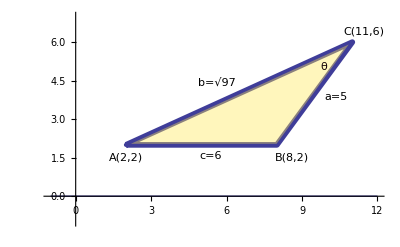

##### Student Workspace

```mathematica
Clear[a,b,c]
```

##### Sample Solution

The Law of Cosines is:  cos(θ)=(a^2+b^2-c^2)/(2a b).  We substitute the given values for a, b, and c into the equation and solve for θ.

```mathematica
Clear[a,b,c]
```

```mathematica
ourequation = Cos[θ] == (a^2 + b^2 - c^2)/(2a*b) /. 
   {a -> 5, b -> √97, c -> 6}
```

```mathematica
N[Solve[ourequation, θ]]
```

We choose the positive value for θ and multiply by 180/π to convert to degrees.

```mathematica
0.509071(180/π)
```

Therefore angle θ is approximately 29.16°.

##### Problem 10.

Given the function f(x)=1/x, find the difference quotient (f(x+h)-f(x))/h. Simplify as much as possible

##### Student Workspace

```mathematica
Clear[f,h]
```

##### Sample Solution

```mathematica
Clear[f,h]
```

```mathematica
f[x_] := 1/x
```

```mathematica
diffquot = (f[x + h] - f[x])/h
```

```mathematica
Simplify[diffquot]
```

##### Problem 11.

Given the points P(1,3) and Q(3,5) do the following:
(a) Find the midpoint M of the line segment joining P and Q. 
(b) Find the distance from P to Q. 
(c) Find the equation of the circle that has P and Q at the end of a diameter.
(d) Create a picture that illustrates the answers you found for parts (a) and (c).

##### Student Workspace

```mathematica
Clear[P,Q,M]
```

##### Sample Solution

```mathematica
Clear[P,Q,M]
```

(a) The coordinates of the midpoint are the averages of the corresponding coordinates for P and Q.

```mathematica
P = {1, 3}
```

```mathematica
Q = {3, 5}
```

```mathematica
M = (P+Q)/2
```

(b) Distance from P to Q is calculated using distance formula.

```mathematica
dist = √((1 - 3)^2 + (3 - 5)^2)
```

(c) Equation of circle is (x-h)^2+(y-k)^2=r^2, where the center is (h,k) and radius is r. Here M is the center and the radius is half the distance from P to Q.

```mathematica
equation = (x - h)^2 + (y - k)^2 == r^2 /. {h -> 2, k -> 4, r -> dist/2}
```

(d) Here is a picture which includes the points P and Q, the midpoint M, the diameter PQ and the required circle. Note that we have added the option AspectRatio -> Automatic to the Show command to get equal scaling on x and y axes so that the circle looks geometrically correct.

```mathematica
circle = ContourPlot[(x - 2)^2 + (y - 4)^2 == 2, {x, -1, 4}, 
    {y, -1, 6}, Axes -> True, Frame -> None]; 
points = ListPlot[{M, P, Q}, PlotStyle -> PointSize[Medium]]; 
diameter = ListLinePlot[{P, Q}, PlotStyle -> Red]; 
Show[circle, points, diameter, AspectRatio -> Automatic]
```

## Additional Graphing Commands (optional)

### Graphing parametric equations -- The ParametricPlot command

The ParametricPlot command is used to graph curves described by parametric equations. 
The basic syntax used to graph a curve described by the parametric equations x=f(t) and y=g(t) on the parameter interval tmin≤t≤tmax is: ParametricPlot[{ f(t), g(t) }, {t,tmin,tmax}]

Plot the curve described by the parametric equations x=t^2-t and y=2t-t^3 over the t-interval [-2,2].

```mathematica
ParametricPlot[{t^2 - t, 2t - t^3}, {t, -2, 2}]
```

##### Exercise A

Plot the curve defined by the equations x=sin(3t) and y=sin(4t) over the t-interval  [0,2π].

Answer to Exercise A

```mathematica
ParametricPlot[{Sin[3t], Sin[4t]}, {t, 0, 2π}]
```

### Graphing polar functions -- The PolarPlot command

The PolarPlot command is used to generate the polar plot of a curve with radius r given as a function of θ. 
The basic syntax used to graph a curve described by the polar equation r=f(θ) on the interval θmin≤θ≤θmax is: PolarPlot[f(θ), {θ,θmin,θmax}]

Plot the curve described by the polar equation r=θ/4 over the θ-interval [0,4π].  Recall that the keyboard shortcut for θ is Esc th Esc.

```mathematica
PolarPlot[θ/4, {θ, 0, 4π}]
```

##### Exercise B

Plot the curve described by the polar equation r=1+cos(θ) over the θ-interval [-π,π].

Answer to Exercise B

```mathematica
PolarPlot[1 + Cos[θ], {θ, -π, π}]
```

## Setting Options for Commands (optional)

At various points during the tutorial we have set specific options for a command. In some cases we find ourselves setting this same option repeatedly. For example, when we use the ContourPlot command we always want to set Axes→True and Frame→None.  The SetOptions command allows you to set these options once for the entire session. This is equivalent to changing the default value for the option.

The basic syntax is:  SetOptions[ command, option→value]. The output is a list of the default values for all options for this command.

Here are some examples.

Example 1. Set the point size to Medium for all ListPlots.

```mathematica
SetOptions[ListPlot, PlotStyle -> PointSize[Medium]]
```

Example 2. Set the options Axes → True and Frame→None for ContourPlot. Notice that we can do both at the same time.

```mathematica
SetOptions[ContourPlot, Axes -> True, Frame -> None]
```